# mass only

### β=1

```mathematica
order=11;
ϵ2=Series[ⅇ^(1/2 Log[ϵ^2/(ϵ^2+(1-ϵ^2)/m2 m1)]),{ϵ,0,order}];
β1=SeriesData[ϵ,0,{1,0,-1},0,order,1];
β2=1-ϵ2^2;
γ1=(1-β1^2)^(-1/2);
γ2=(1-β2^2)^(-1/2);
```

```mathematica
ω=Simplify[Series[T/(γ1^2 β1 m1),{ϵ,0,order}],ϵ>0 && m1>0 && m2>0];
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2),ϵ>0 && m1>0 && m2>0];
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω,ϵ>0 && m1>0 && m2>0];
```

```mathematica
ϵp=InverseSeries[H,En];
Simplify[ComposeSeries[J,ϵp]/.{m1->m,m2->m},m>0]/. {T->1/(2π α)}
```

α En^2-8/3 (m^(3/2) √π α) √En+2/5 m^(5/2) π^(3/2) α √(1/En)+O[1/En]^1

```mathematica
Normal[%]
```

En^2 α-(8 m^(3/2) √π α)/(3 √(1/En))+2/5 √(1/En) m^(5/2) π^(3/2) α

```mathematica
ϵp=InverseSeries[H];
Simplify[ComposeSeries[J,ϵp]/(α ϵ^2) ,{m1>0,m2>0}]/. {ϵ-> En,T->1/(2π α)}
```

1-4/3 ((m1^(3/2)+m2^(3/2)) √π) (1/En)^(3/2)+1/5 (m1^(5/2)+m2^(5/2)) π^(3/2) (1/En)^(5/2)+O[1/En]^3

### β->0

```mathematica
order=5;
β2=Simplify[Series[β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2]],{β1,0,order}],m2>0];
γ1=Series[(1-β1^2)^(-1/2),{β1,0,order}];
γ2=(1-β2^2)^(-1/2);
```

```mathematica
ω=Simplify[Series[ T/(γ1^2 β1 m1),{β1,0,order}],β1>0 && m1>0 && m2>0];
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2),β1>0 && m1>0 && m2>0];
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω,β1>0 && m1>0 && m2>0];
```

```mathematica
βp=InverseSeries[H,En];
traj=Simplify[ComposeSeries[J,βp] ,{m1>0,m2>0}]/. {T->1/(2π α)}
```

4/3 √(2/3) √((m1 m2)/(m1+m2)) π α (En-m1-m2)^(3/2)+(7 √(2/3) (m1^2-m1 m2+m2^2) π α (En-m1-m2)^(5/2))/(27 √(m1 m2 (m1+m2)^3))+O[En-m1-m2]^(7/2)

```mathematica
Normal[Simplify[traj/.{m1-> m,m2->m},m>0]]
```

(7 (En-2 m)^(5/2) π α)/(54 √3 √m)+(4 (En-2 m)^(3/2) √m π α)/(3 √3)

```mathematica
Simplify[%,m>0]
```

((En-2 m)^(3/2) (7 En+58 m) π α)/(54 √3 √m)

### β=0

```mathematica
order=5;
β2=Simplify[Series[β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2]],{β1,0,order}],m2>0];
γ1=Series[(1-β1^2)^(-1/2),{β1,0,order}];
γ2=(1-β2^2)^(-1/2);
```

```mathematica
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2),β1>0 && m1>0 && m2>0]
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω,β1>0 && m1>0 && m2>0]
```

(m1+m2)+((m1+m2) T β1)/(m2 ω)+(m1 (m1+m2) β1^2)/(2 m2)+((-5 m1^3+6 m1 m2^2+m2^3) T β1^3)/(6 m2^3 ω)+1/8 m1 (3-(5 m1^3)/m2^3+(8 m1)/m2) β1^4+((63 m1^5-100 m1^3 m2^2+40 m1 m2^4+3 m2^5) T β1^5)/(40 m2^5 ω)+O[β1]^6

(m1 (m1+m2) β1^2)/(m2 ω)+((m1^3+m2^3) T β1^3)/(3 m2^3 ω^2)+(m1 (-3 m1^3+4 m1 m2^2+m2^3) β1^4)/(2 m2^3 ω)+((-9 m1^5+10 m1^3 m2^2+m2^5) T β1^5)/(10 m2^5 ω^2)+O[β1]^6

```mathematica
H/. {m1-> m, m2-> m}
J/. {m1-> m, m2-> m}
```

2 m+(2 T β1)/ω+m β1^2+(T β1^3)/(3 ω)+(3 m β1^4)/4+(3 T β1^5)/(20 ω)+O[β1]^6

(2 m β1^2)/ω+(2 T β1^3)/(3 ω^2)+(m β1^4)/ω+(T β1^5)/(5 ω^2)+O[β1]^6

```mathematica
βp=InverseSeries[H];
Simplify[ComposeSeries[J,βp] /.{m1->m,m2->m},m>0]/. {β1-> En,T->1/(2π α)}
```

2 m π^2 α^2 ω (En-2 m)^2+4/3 π^4 α^4 ω (1/(4 π^2 α^2)-3 m^2 ω^2) (En-2 m)^3+2/3 m π^6 α^6 ω^3 (-1/(π^2 α^2)+15 m^2 ω^2) (En-2 m)^4-4/15 (π^8 α^8 (ω^3/(4 π^4 α^4)+105 m^4 ω^7)) (En-2 m)^5+O[En-2 m]^6

# Charge and mass

## Retardation angle

### β=1

```mathematica
ϵ2=Series[ⅇ^(1/2 Log[ϵ^2/(ϵ^2+(1-ϵ^2)/m2 m1)]),{ϵ,0,5}];
β1=SeriesData[ϵ,0,{1,0,-1},0,5,1];
β2=1-ϵ2^2;
γ1=(1-β1^2)^(-1/2);
γ2=(1-β2^2)^(-1/2);
θ=SeriesData[ϵ,0,{a0,a1,a2,a3,a4},0,5,1];
```

```mathematica
θeq=θ^2-β1^2-β2^2-2β1 β2 Cos[θ] ;
a0=a0/.FindRoot[SeriesCoefficient[θeq,0]==0,{a0,1}];
a1=a1/.Solve[SeriesCoefficient[θeq,1]==0,a1][[1]];
a2=a2/.Solve[SeriesCoefficient[θeq,2]==0,a2][[1]];
a3=a3/.Solve[SeriesCoefficient[θeq,3]==0,a3][[1]];
a4=a4/.Solve[SeriesCoefficient[θeq,4]==0,a4][[1]];
```

```mathematica
(*ω=Simplify[Series[ωω/.Solve[Normal[γ1 β1 m1 ωω+(q^2 ωω^2)/(θ(β1  β2 Sin[θ]+θ)^3)(β1 β2 (β2 θ+β1^3 Sin[θ]+β2 β1^2(θ+Sin[2θ]))+β1^2 β2(β2^2(Sin[θ]+θ Cos[θ])+θ Cos[θ])+θ(β1(1-β2^2 Cos[θ]^2)+β2(θ Sin[θ])+Cos[θ](1-β2^2)))-T/γ1]==0,ωω][[2]],{ϵ,0,5}],ϵ>0 && m1>0 && m2>0];*)
ω=Simplify[Series[ωω/.Solve[Normal[-T √(1-β1^2)+(m1 β1 ωω)/(√(1-β1^2))-(q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)]==0,ωω][[1]],{ϵ,0,5}],ϵ>0 && m1>0 && m2>0];
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2)+q^2 ω(1/(β1 β2 Sin[θ]+θ)),ϵ>0 && m1>0 && m2>0];
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω-2 q^2 β1 β2 Cos[θ]/(β1 β2 Sin[θ]+θ),ϵ>0 && m1>0 && m2>0];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
FullSimplify[Solve[Normal[-T √(1-β1^2)+(m1 β1 ωω)/(√(1-β1^2))-(q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)]==0,ωω][[1]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{ωω→1/(q^2 ϵ)(m1 (-0.87465+0.655987 ϵ^2)-0.0000160558 √(1.35715×10^10 q^2 T ϵ^3+m1^2 (2.96758×10^9-4.45137×10^9 ϵ^2+1.66926×10^9 ϵ^4)))}

```mathematica
Simplify[m1(γ1 β1^2)/ω,ϵ>0 && m1>0 && m2>0]
```

-0.404223 q^2+0.404223 q^2 ϵ^2+O[ϵ]^3

```mathematica
ϵp=InverseSeries[H];
Simplify[ComposeSeries[J,ϵp] ,m>0]/. {ϵ-> En,T->1/(2π α)}
```

((-0.478999 m1-0.404223 √(m1 m2)) q^2)/m1+(0.0394158 (1.57009×10^-16-1. √(m2/m1))^2 q^2 (1. m1^2-4.12768 m1 m2-1.28192 √(m1^3 m2)+6.4096 √(m1 m2^3)+(1.03636 q^2)/α))/En^2+O[1/En]^3

```mathematica
H
```

(m1 (-1.11022×10^-16+0.707107 √(m2/m1)))/ϵ+(0.284603 m1-0.422503 m2+(0.53033 m2^(3/2))/(√m1)-0.353553 √(m1 m2)-(1.79591 q^2 T)/m1) ϵ+O[ϵ]^2

```mathematica
J
```

((-3.18453×10^15 m1-0.0747761 m2-3.18453×10^15 √(m1 m2)) q^2)/m2+1/(m1 m2^2)q^2 (3.98066×10^15 m1^2 m2-0.325391 m1 m2^2-0.325391 m2^3+0.25 (m1 m2)^(3/2)+3.98066×10^15 √(m1 m2^5)+3.18595×10^31 m1 q^2 T) ϵ^2+O[ϵ]^3

### β->0

```mathematica
order=9;
β2=Simplify[Series[β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2]],{β1,0,order}],m2>0&&m1>0];
γ1=Series[(1-β1^2)^(-1/2),{β1,0,order}];
γ2=(1-β2^2)^(-1/2);
θ=SeriesData[β1,0,{0,a1,a2,a3,a4,a5,a6,a7,a8},0,order,1];
```

```mathematica
θeq=θ^2-β1^2-β2^2-2β1 β2 Cos[θ];
a1=a1/.Solve[SeriesCoefficient[θeq,2]==0,a1][[2]];
a2=a2/.Solve[SeriesCoefficient[θeq,3]==0,a2][[1]];
a3=a3/.Solve[SeriesCoefficient[θeq,4]==0,a3][[1]];
a4=a4/.Solve[SeriesCoefficient[θeq,5]==0,a4][[1]];
a5=a5/.Solve[SeriesCoefficient[θeq,6]==0,a5][[1]];
a6=a6/.Solve[SeriesCoefficient[θeq,7]==0,a6][[1]];
a7=a7/.Solve[SeriesCoefficient[θeq,8]==0,a7][[1]];
a8=a8/.Solve[SeriesCoefficient[θeq,9]==0,a8][[1]];
```

```mathematica
ω=Simplify[Series[ωω/.Solve[Normal[-T √(1-β1^2)+(m2 β1 ωω)/(√(1-β1^2))-(q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)]==0,ωω][[1]],{β1,0,order}],β1>0 && m1>0 && m2>0];
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2)+q^2 ω (1/(β1 β2 Sin[θ]+θ)),β1>0 && m1>0 && m2>0];
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω-2 q^2 β1 β2 Cos[θ]/(β1 β2 Sin[θ]+θ),β1>0 && m1>0 && m2>0];
```

```mathematica
βp=InverseSeries[H];
FullSimplify[ComposeSeries[J,βp]/. {β1-> En,m1->m,m2->m} ,{m>0}]
```

```mathematica
-((5 q^2 T+6 m √(q^2 T)) √(En-2 m+2 √(q^2 T)))/(2 (√3 T √(3 m+√(q^2 T))))+(3 √3 (120 m^3+573 m q^2 T-50 m^2 √(q^2 T)+109 (q^2 T)^(3/2)) (En-2 m+2 √(q^2 T))^(3/2))/(80 T (3 m+√(q^2 T))^(5/2))+1/(44800 (q^2 T)^(3/2) (3 m+√(q^2 T))^(9/2))√3 q^2 (453600 m^5+14798070 m^3 q^2 T+1899444 m q^4 T^2-1965600 m^4 √(q^2 T)-27263115 m^2 (q^2 T)^(3/2)+503969 (q^2 T)^(5/2)) (En-2 m+2 √(q^2 T))^(5/2)+O[En-2 m+2 √(q^2 T)]^(7/2)/.q->0
```

(√m (En-2 m)^(3/2))/(2 T)+Indeterminate (En-2 m)^(5/2)+O[En-2 m]^(7/2)

```mathematica
H
```

(m1+m2-2 √(q^2 T))+1/6 (3 m1+3 m2+2 √(q^2 T)) β1^2+((3 m1)/8+(25 m2)/24-m2^2/(√(q^2 T))-(19 √(q^2 T))/20) β1^4+((5 m1)/16+(1243 m2)/240-(11 m2^2)/(6 √(q^2 T))-(19 √(q^2 T))/504) β1^6+O[β1]^8

# Charge, mass and casimir

### β=1

```mathematica
(*ϵ2=Series[ⅇ^(1/2 Log[ϵ^2/(ϵ^2+(1-ϵ^2)/m2 m1)]),{ϵ,0,5}];*)
(*β2=1-ϵ2^2;*)
```

```mathematica
order=10;
β1=Series[1-ϵ^2,{ϵ,0,order}];
β2=SeriesData[ϵ,0,Table[b[i],{i,1,2order}],0,2order,1];
β2=β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,Table[b[i],{i,1,2order}]][[2]];
γ1=(1-β1^2)^(-1/2);
γ2=(1-β2^2)^(-1/2);
θ=SeriesData[ϵ,0,Prepend[Table[a[i],{i,2,order}],a[1]],0,order,1];
θeq=θ^2-β1^2-β2^2-2β1 β2 Cos[θ] ;
a[1]=a[1]/.FindRoot[SeriesCoefficient[θeq,0]==0,{a[1],1}];
θ=FullSimplify[θ/.Solve[θeq-SeriesCoefficient[θeq,0]==0,Table[a[i],{i,2,order}]][[1]]];
```

```mathematica
ω=Simplify[Series[ωω/.Solve[Normal[-T √(1-β1^2)+(m1 β1 ωω)/(√(1-β1^2))-Rationalize[(q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3),10^-5]-π/2((a-S) ωω^2)/(β1+β2)^2]==0,ωω][[1]],{ϵ,0,order}],ϵ>0 && m1>0 && m2>0];
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2)+q^2 ω Rationalize[(1/(β1 β2 Sin[θ]+θ)),10^-5]-π/2((a-S) ω)/(β1+β2),ϵ>0 && m1>0 && m2>0];
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω-2 q^2 β1 β2 Rationalize[Cos[θ]/(β1 β2 Sin[θ]+θ),10^-5],ϵ>0 && m1>0 && m2>0];
ϵp=InverseSeries[H,En];
traj=FullSimplify[ComposeSeries[J,ϵp],{m1>0,m2>0}]/. {T-> 1/(2π α)};
```

```mathematica
Normal[α En^2-4/3 ((m1^(3/2)+m2^(3/2)) √π α) √En+(-(26753 q^2)/55854+1/4 π (a-S))+1/5 (m1^(5/2)+m2^(5/2)) π^(3/2) α √(1/En)+O[1/En]^1]
```

```mathematica
-0.479 q^2+1/4 π(a-S)+α E^2-(4 (m1^(3/2)+m2^(3/2)) √π α)/3 √E+(π^(3/2)α)/5 (m1^(5/2)+m2^(5/2))/(√E)
```

### β->0

```mathematica
order=6;
β2=Simplify[Series[β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2]],{β1,0,order}],m2>0];
γ1=Series[(1-β1^2)^(-1/2),{β1,0,order}];
γ2=(1-β2^2)^(-1/2);
θ=SeriesData[β1,0,Table[a[i],{i,order}],1,order,1];
θeq=θ^2-β1^2-β2^2-2β1 β2 Cos[θ];
θ=FullSimplify[θ/.Solve[θeq==0,Table[a[i],{i,1,order}]]][[1]];
```

```mathematica
ω=Simplify[Series[ωω/.Solve[Normal[-T √(1-β1^2)+(m1 β1 ωω)/(√(1-β1^2))-(q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)-π/2((a-S) ωω^2)/(β1+β2)^2]==0,ωω][[1]],{β1,0,order}],β1>0 && m1>0 && m2>0&&T>0];
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2)+q^2 ω (1/(β1 β2 Sin[θ]+θ))-π/2((a-S) ω)/(β1+β2),β1>0 && m1>0 && m2>0&&T>0];
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω-2 q^2 β1 β2 Cos[θ]/(β1 β2 Sin[θ]+θ),β1>0 && m1>0 && m2>0&&T>0];
βp=InverseSeries[H,En];
traj=ComposeSeries[J,βp];
```

```mathematica
FullSimplify[SeriesCoefficient[traj,1/2]/.{m1->m,m2->m},T>0]
```

(√((√((-a π-2 q^2+π S) T))/(3 √2 (a π-4 q^2-π S) T+36 m √((-a π-2 q^2+π S) T))) (-a π T+10 q^2 T+π S T-6 √2 m √((-a π-2 q^2+π S) T)))/(2 T)

```mathematica
FullSimplify[SeriesCoefficient[traj,3/2]/.{m1->m,m2->m},T>0]
```

(3 (-80 √2 m^2 (10 q^2-11 π S) (2 q^2-π S) T+12 m √(-a π-2 q^2+π S) (1528 q^4-748 π q^2 S+17 π^2 S^2) T^(3/2)+7 √2 a^3 π^3 T^2+√2 (-3488 q^6+200 π q^4 S+726 π^2 q^2 S^2-7 π^3 S^3) T^2+1920 m^3 (-2 q^2+π S) √((-a π-2 q^2+π S) T)+a^2 π^2 T (-880 √2 m^2+3 √2 (242 q^2-7 π S) T+204 m √((-a π-2 q^2+π S) T))+a π (160 √2 m^2 (-16 q^2+11 π S) T+408 m (22 q^2-π S) √(-a π-2 q^2+π S) T^(3/2)+√2 (-200 q^4-1452 π q^2 S+21 π^2 S^2) T^2-1920 m^3 √((-a π-2 q^2+π S) T))))/(40 (√2 (a π-4 q^2-π S) T+12 m √((-a π-2 q^2+π S) T))^3 √((√((-a π-2 q^2+π S) T))/(3 √2 (a π-4 q^2-π S) T+36 m √((-a π-2 q^2+π S) T))))

```mathematica
FullSimplify[SeriesCoefficient[traj,-3/2]/.{m1->m,m2->m},T>0]
```

0

```mathematica
Simplify[En-(√2 a π T+2 √2 q^2 T-√2 π S T+2 m √((-a π-2 q^2+π S) T))/(√(-(a π+2 q^2-π S) T))]
```

```mathematica
E-2 m+√2 √(-(a π+2 q^2-π S) T)
```

```mathematica
Simplify[Series[FullSimplify[SeriesCoefficient[traj,3/2]/.{m1->m,m2->m,a->1,S->1},T>0&&S>0],{q,0,2}]]
```

1/(2 √(1/m) T)+(5 √(1/m) q)/(8 √-T)-673/240 (1/m)^(3/2) q^2+O[q]^3

```mathematica
Series[FullSimplify[SeriesCoefficient[traj,3/2]/.{m1->m,m2->m,a->1,S->1,T->1/(2π α)},α>0&&S>0],{q,0,2}]
```

m π √(1/(m α)) α^(3/2)-5/24 ⅈ √π (-2 ⅈ √2 √(1/(m α)) √-α+√2 √(1/(m α)) √α) √α q+((125 ⅈ √(1/(m α)) √-α-1894 √(1/(m α)) √α) q^2)/(720 m)+O[q]^3

### β=0

```mathematica
order=7;
β2=Simplify[Series[β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2]],{β1,0,order}],m2>0]/.{m1->m,m2->m};
γ1=Series[(1-β1^2)^(-1/2),{β1,0,order}];
γ2=(1-β2^2)^(-1/2);
θ=SeriesData[β1,0,{0,a1,a2,a3,a4,a5},0,order,1];
```

```mathematica
θeq=θ^2-β1^2-β2^2-2β1 β2 Cos[θ];
a1=a1/.Solve[SeriesCoefficient[θeq,2]==0,a1][[2]];
a2=a2/.Solve[SeriesCoefficient[θeq,3]==0,a2][[1]];
a3=a3/.Solve[SeriesCoefficient[θeq,4]==0,a3][[1]];
a4=a4/.Solve[SeriesCoefficient[θeq,5]==0,a4][[1]];
a5=a5/.Solve[SeriesCoefficient[θeq,6]==0,a5][[1]];
```

```mathematica
Simplify[-T √(1-β1^2)+(m1 β1 ω)/(√(1-β1^2))-(q^2 ω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)-(a ω^2)/(β1+β2)^2/.{ω->β1/l},β1>0 && m1>0 && m2>0]
H=Simplify[T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2)+q^2 ω (1/(β1 β2 Sin[θ]+θ))-(a ω)/(β1+β2),β1>0 && m1>0 && m2>0]/.{ω->β1/l}
J=Simplify[T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω-2 q^2 β1 β2 Cos[θ]/(β1 β2 Sin[θ]+θ),β1>0 && m1>0 && m2>0]/.{ω->β1/l}
```

-(a-q^2+4 l^2 T)/(4 l^2)+(m1/l-q^2/(8 l^2)+T/2) β1^2+O[β1]^4

(-a/(2 l)+m1+m2+q^2/(2 l)+2 l T)+(m1/2+m2/2-q^2/(4 l)+(l T)/3) β1^2+((3 m1)/8+(3 m2)/8+(7 q^2)/(16 l)) β1^4+O[β1]^5

(l m1+l m2-q^2+(2 l^2 T)/3) β1+1/10 (5 l m1+5 l m2+25 q^2+2 l^2 T) β1^3+1/24 (9 l m1+9 l m2-109 q^2) β1^5+O[β1]^7

# analyze ω

### β->0

```mathematica
order=9;
β2=Simplify[Series[β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2]],{β1,0,order}],m2>0]/.{m1->m,m2->m};
γ1=Series[(1-β1^2)^(-1/2),{β1,0,order}];
γ2=(1-β2^2)^(-1/2);
θ=SeriesData[β1,0,{0,a1,a2,a3,a4,a5,a6,a7,a8},0,order,1];
```

```mathematica
θeq=θ^2-β1^2-β2^2-2β1 β2 Cos[θ];
a1=a1/.Solve[SeriesCoefficient[θeq,2]==0,a1][[2]];
a2=a2/.Solve[SeriesCoefficient[θeq,3]==0,a2][[1]];
a3=a3/.Solve[SeriesCoefficient[θeq,4]==0,a3][[1]];
a4=a4/.Solve[SeriesCoefficient[θeq,5]==0,a4][[1]];
a5=a5/.Solve[SeriesCoefficient[θeq,6]==0,a5][[1]];
a6=a6/.Solve[SeriesCoefficient[θeq,7]==0,a6][[1]];
a7=a7/.Solve[SeriesCoefficient[θeq,8]==0,a7][[1]];
a8=a8/.Solve[SeriesCoefficient[θeq,9]==0,a8][[1]];
```

```mathematica
ω=Simplify[Solve[Normal[-T √(1-β1^2)+(m2 β1 ωω)/(√(1-β1^2))-(q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)+O[β1]]==0,ωω],β1>0 && m1>0 && m2>0]
```

{{ωω→-(2 √2 √T β1)/(√(-q^2 (-2+β1^2)))},{ωω→(2 √2 √T β1)/(√(-q^2 (-2+β1^2)))}}

```mathematica
-T √(1-β1^2)+(m2 β1 ωω)/(√(1-β1^2))-(q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)
```

### β=1

```mathematica
order=6;
ϵ2=Series[ⅇ^(1/2 Log[ϵ^2/(ϵ^2+(1-ϵ^2)/m2 m1)]),{ϵ,0,order}];
β1=SeriesData[ϵ,0,{1,0,-1},0,order,1];
β2=1-ϵ2^2;
γ1=(1-β1^2)^(-1/2);
γ2=(1-β2^2)^(-1/2);
θ=SeriesData[ϵ,0,{a0,a1,a2,a3,a4},0,order,1];
```

```mathematica
θeq=θ^2-β1^2-β2^2-2β1 β2 Cos[θ] ;
a0=a0/.FindRoot[SeriesCoefficient[θeq,0]==0,{a0,1}];
a1=a1/.Solve[SeriesCoefficient[θeq,1]==0,a1][[1]];
a2=a2/.Solve[SeriesCoefficient[θeq,2]==0,a2][[1]];
a3=a3/.Solve[SeriesCoefficient[θeq,3]==0,a3][[1]];
a4=a4/.Solve[SeriesCoefficient[θeq,4]==0,a4][[1]];
```

```mathematica
Series[Simplify[ωω/.Solve[Normal[-T √(1-β1^2)+(m1 β1 ωω)/(√(1-β1^2))-(-q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(-q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)==0],ωω],ϵ>0 && m1>0 && m2>0&&m>0][[1]]/.{m1->m,m2->m},{ϵ,0,4}]
```

((0.87465 m)/q^2-(0.87465 √(m^4))/(m q^2))/ϵ+(-(1.53064 m)/q^2+(1.53064 √(m^4))/(m q^2)) ϵ+(2. √(m^4) T ϵ^2)/m^3+((1.53064 m)/q^2-(1.53064 √(m^4))/(m q^2)) ϵ^3+(1.5 √(m^4) T ϵ^4)/m^3+O[ϵ]^5

```mathematica
Simplify[%,m>0]
```

(2. T ϵ^2)/m+(1.5 T ϵ^4)/m+O[ϵ]^5

```mathematica
Series[Simplify[ωω/.Solve[Normal[-T √(1-β1^2)+(m1 β1 ωω)/(√(1-β1^2))-(-q^2 ωω^2 (-2 β1+β1 β2^2+2 β2 (-1+β2^2) Cos[θ]+β1 β2^2 Cos[2 θ]-2 β2 θ Sin[θ]))/(2 (θ+β1 β2 Sin[θ])^3)+(-q^2 β1 β2 ωω^2 (β1 (1+β2^2) θ Cos[θ]+β1 (β1^2+β2^2) Sin[θ]+β2 (θ+β1^2 θ+β1^2 Sin[2 θ])))/(θ (θ+β1 β2 Sin[θ])^3)==0],ωω],ϵ>0 && m1>0 && m2>0&&m>0][[2]]/.{m1->m,m2->m},{ϵ,0,4}]
```

((0.87465 m)/q^2+(0.87465 √(m^4))/(m q^2))/ϵ+(-(1.53064 m)/q^2-(1.53064 √(m^4))/(m q^2)) ϵ-(2. (√(m^4) T) ϵ^2)/m^3+((1.53064 m)/q^2+(1.53064 √(m^4))/(m q^2)) ϵ^3-(1.5 (√(m^4) T) ϵ^4)/m^3+O[ϵ]^5

```mathematica
Simplify[%,m>0]
```

(1.7493 m)/(q^2 ϵ)-(3.06127 m ϵ)/q^2-(2. T ϵ^2)/m+(3.06127 m ϵ^3)/q^2-(1.5 T ϵ^4)/m+O[ϵ]^5

# perturbation analysis in ã and α_e

## definitions

### series definitions

x is the casimir coefficient
z is the fine structure constant

```mathematica
β2[β1_]:=SeriesData[x,0,Table[SeriesData[z,0,Table[y[β1,i,j],{j,1,2}],0,2,1],{i,1,2}],0,2,1];
Δθ[β1_] :=SeriesData[x,0,Table[SeriesData[z,0,Table[th[β1,i,j],{j,1,2}],0,2,1],{i,1,2}],0,2,1];
ω[β1_] :=SeriesData[x,0,Table[SeriesData[z,0,Table[w[β1,i,j],{j,1,2}],0,2,1],{i,1,2}],0,2,1];
```

```mathematica
(*cut off the 2nd degree terms for now*)
y[β1_,2,2]=th[β1_,2,2]=w[β1_,2,2]=0;
```

### equations definitions

```mathematica
θeq[β1_]:=Δθ[β1]^2-β1^2-β2[β1]^2-2β1 β2[β1] Cos[Δθ[β1]];
eq1[β1_,m1_,m2_,α_,q1_,q2_]:=1/(2π α) √(1-β1^2)-(m1 β1 ω[β1])/(√(1-β1^2))+(π x ω[β1]^2)/(2 (β1+β2[β1])^2)-(z q1 q2 ω[β1]^2 (β1+2 β1 β2[β1]^2+β1^3 β2[β1]^2+β2[β1] (1+β1^2 (2+β2[β1]^2)) Cos[Δθ[β1]]+(1+β1^2) β2[β1] Δθ[β1] Sin[Δθ[β1]]))/(Δθ[β1]+β1 β2[β1] Sin[Δθ[β1]])^3;
eq2[β1_,m1_,m2_,α_,q1_,q2_]:=1/(2π α) √(1-β2[β1]^2)-(m2 β2[β1] ω[β1])/(√(1-β2[β1]^2))+(π x ω[β1]^2)/(2 (β1+β2[β1])^2)-(z q1 q2 ω[β1]^2 (β2[β1]+2 β1^2 β2[β1]+β1^2 β2[β1]^3+β1 (1+(2+β1^2) β2[β1]^2) Cos[Δθ[β1]]+β1 (1+β2[β1]^2) Δθ[β1] Sin[Δθ[β1]]))/(Δθ[β1]+β1 β2[β1] Sin[Δθ[β1]])^3;
H[β1_,m1_,m2_,α_,q1_,q2_]:=1/ω[β1] 1/(2π α)(ArcSin[β1]+ArcSin[β2[β1]])+m1/(√(1-β1^2))+m2/(√(1-β2[β1]^2))+z q1 q2 ω[β1] (1/(β1 β2[β1] Sin[Δθ[β1]]+Δθ[β1]))-π/2(x ω[β1])/(β1+β2[β1]);
J[β1_,m1_,m2_,α_,q1_,q2_]:=1/(2π α)(-β1 √(1-β1^2)+ArcSin[β1]-β2[β1] √(1-β2[β1]^2)+ArcSin[β2[β1]])/(2 ω[β1]^2)+m1 β1^2/(ω[β1] √(1-β1^2))+m2 β2[β1]^2/(ω[β1] √(1-β2[β1]^2))-2z q1 q2 β1 β2[β1] Cos[Δθ[β1]]/(β1 β2[β1] Sin[Δθ[β1]]+Δθ[β1]);
```

### handling ω and β_2

```mathematica
E111[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq1[β1,m1,m2,α,q1,q2],{0,0}];
E211[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq2[β1,m1,m2,α,q1,q2],{0,0}];
s0[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[E111[β1,m1,m2,α,q1,q2]==0&&E211[β1,m1,m2,α,q1,q2]==0,{w[β1,1,1],y[β1,1,1]}][[2]]//Simplify;
```

```mathematica
E121[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq1[β1,m1,m2,α,q1,q2],{1,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
E221[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq2[β1,m1,m2,α,q1,q2],{1,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
E112[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq1[β1,m1,m2,α,q1,q2],{0,1}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
E212[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq2[β1,m1,m2,α,q1,q2],{0,1}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
s21[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[E121[β1,m1,m2,α,q1,q2]==0&&E221[β1,m1,m2,α,q1,q2]==0,{w[β1,2,1],y[β1,2,1]}][[1]]//Simplify;
s12[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[E112[β1,m1,m2,α,q1,q2]==0&&E212[β1,m1,m2,α,q1,q2]==0,{w[β1,1,2],y[β1,1,2]}][[1]]//Simplify;
```

### handling Δθ

```mathematica
T11[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[θeq[β1],{0,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
T12[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[θeq[β1],{0,1}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
T21[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[θeq[β1],{1,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
```

```mathematica
thsol12[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[T12[β1,m1,m2,α,q1,q2]==0,th[β1,1,2]][[1]];
thsol21[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[T21[β1,m1,m2,α,q1,q2]==0,th[β1,2,1]][[1]];
```

```mathematica
thsol11[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ]:=Solve[T11[β1,m1,m2,α,q1,q2]==0&&  0≤ th[β1,1,1],{th[β1,1,1]}][[1,1]];
```

```mathematica
(*ListPlot[Table[{r,thsol11[r,150,150,0.9 10^-6,1/3,-1/3][[2]]},{r,0.01,0.99,0.01}]]*)
```

### overall solution

```mathematica
solall[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=Flatten[{s0[β1,m1,m2,α,q1,q2],s12[β1,m1,m2,α,q1,q2],s21[β1,m1,m2,α,q1,q2],thsol11[β1,m1,m2,α,q1,q2],thsol12[β1,m1,m2,α,q1,q2],thsol21[β1,m1,m2,α,q1,q2],x->x1,z->1/137}];

solall[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=Flatten[{s0[β1,m1,m2,α,q1,q2],s12[β1,m1,m2,α,q1,q2],s21[β1,m1,m2,α,q1,q2],thsol12[β1,m1,m2,α,q1,q2],thsol21[β1,m1,m2,α,q1,q2],x->x1,z->1/137}];

solall[β1_,m1_,m2_,α_,q1_,q2_]:=Flatten[{s0[β1,m1,m2,α,q1,q2],s12[β1,m1,m2,α,q1,q2],s21[β1,m1,m2,α,q1,q2],thsol12[β1,m1,m2,α,q1,q2],thsol21[β1,m1,m2,α,q1,q2]}];

AngularMomentum[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=ReplaceRepeated[Normal[J[β1,m1,m2,α,q1,q2]],solall[β1,m1,m2,α,q1,q2,x1]];
Energy[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=ReplaceRepeated[Normal[H[β1,m1,m2,α,q1,q2]],solall[β1,m1,m2,α,q1,q2,x1]];
(*approximately find velocity for given J*)
(*vJ[J_,m1_,m2_,α_,q1_,q2_,x1_]:=Block[{v,data,Jint},
data=Table[{v,AngularMomentum[v,m1,m2,α,q1,q2,x1]},{v,10^-5,1-10^-5,(1-2 10^-5)/5}];
Jint=Interpolation[data];
v=0.5;
While[Abs[J-Jint[v]]>10^-AccuracyGoal+Abs[J] 10^-PrecisionGoal
,]
v/.NSolve[==J&&0<v< 1,v]]*)
(*returns interpolation of trajectory*)
ReggeInterpolation[m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=Block[{β1},
Interpolation[DeleteCases[Table[{Energy[β1,m1,m2,α,q1,q2,x1],AngularMomentum[β1,m1,m2,α,q1,q2,x1]},{β1,0.01,0.99,0.02}],{E_,J_}/;J<0]]]
```

### generate regge points

```mathematica
PlotRegge[β1min_,β1max_,m1_,m2_,α_,q1_,q2_,x1_]:=ListPlot[Evaluate[Table[ReplaceRepeated[Normal[{J[v,m1,m2,α,q1,q2],H[v,m1,m2,α,q1,q2]}],solall[v,m1,m2,α,q1,q2,x1]]
,{v,β1min,β1max,(β1max-β1min)/10}]]]
```

```mathematica
point[j_,m1_,m2_,α_,q1_,q2_,x1_]:=Block[{v},v=vJ[j,m1,m2,α,q1,q2,x1]
ReplaceRepeated[Normal[{Energy[v,m1,m2,α,q1,q2]^2,j}],{z->1/137,x-> x1}]]
```

## calculations

### Check error magnitude (in next order of pert.)

```mathematica
ss=eq1[β1,m1,m2,α,q1,q2]/.solall[β1,m1,m2,α,q1,q2];
```

```mathematica
Simplify[Series[SeriesCoefficient[ss,{1,1}],{β1,0,0}],m1>0&&m2>0&&α>0]
```

ComplexInfinity/β1^3+ComplexInfinity/β1^2+ComplexInfinity/β1+ComplexInfinity+O[β1]^1

```mathematica
ReplaceAll[ss,th[xx_,1,1]->xx]
```

(m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2))/(2 m1 β1)-(x1 (-1+β1^2)^2 (m2^3 √(2-2 β1^2) (-1+β1^2)^2+m2^2 √(2-2 β1^2) (-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-m1^2 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^2 m2 β1^2 (2 √(2-2 β1^2)+√(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))))/(√2 m1 α β1 (2 m1 β1^2+m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2))^2 (4 m1^2 β1^2+m2^2 (-1+β1^2)^2+m2 (-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))+(2 √2 q1 q2 (-1+β1^2)^2 (2 m1 m2^5 √(2-2 β1^2)+9 m1^3 m2^3 β1^2 √(2-2 β1^2)-7 m1 m2^5 β1^2 √(2-2 β1^2)+6 m1^5 m2 β1^4 √(2-2 β1^2)-14 m1^3 m2^3 β1^4 √(2-2 β1^2)+8 m1 m2^5 β1^4 √(2-2 β1^2)+2 m1^5 m2 β1^6 √(2-2 β1^2)+m1^3 m2^3 β1^6 √(2-2 β1^2)-2 m1 m2^5 β1^6 √(2-2 β1^2)+4 m1^3 m2^3 β1^8 √(2-2 β1^2)-2 m1 m2^5 β1^8 √(2-2 β1^2)+m1 m2^5 β1^10 √(2-2 β1^2)-2 m1 m2^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-5 m1^3 m2^2 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+5 m1 m2^4 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+3 m1^3 m2^2 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-3 m1 m2^4 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+2 m1^3 m2^2 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-m1 m2^4 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+m1 m2^4 β1^8 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-m1^4 m2^2 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^4 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-2 m1^6 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-4 m1^4 m2^2 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+4 m1^2 m2^4 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-6 m1^6 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+11 m1^4 m2^2 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-6 m1^2 m2^4 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-6 m1^4 m2^2 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+4 m1^2 m2^4 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^4 β1^10 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^4 m2 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^2 m2^3 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+3 m1^4 m2 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-3 m1^2 m2^3 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-4 m1^4 m2 β1^6 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+3 m1^2 m2^3 β1^6 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^3 β1^8 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^4 √(2-2 β1^2) Cos[β1]-m2^6 √(2-2 β1^2) Cos[β1]-3 m1^4 m2^2 β1^2 √(2-2 β1^2) Cos[β1]-4 m1^2 m2^4 β1^2 √(2-2 β1^2) Cos[β1]+5 m2^6 β1^2 √(2-2 β1^2) Cos[β1]-8 m1^4 m2^2 β1^4 √(2-2 β1^2) Cos[β1]+18 m1^2 m2^4 β1^4 √(2-2 β1^2) Cos[β1]-10 m2^6 β1^4 √(2-2 β1^2) Cos[β1]+11 m1^4 m2^2 β1^6 √(2-2 β1^2) Cos[β1]-20 m1^2 m2^4 β1^6 √(2-2 β1^2) Cos[β1]+10 m2^6 β1^6 √(2-2 β1^2) Cos[β1]+7 m1^2 m2^4 β1^8 √(2-2 β1^2) Cos[β1]-5 m2^6 β1^8 √(2-2 β1^2) Cos[β1]+m2^6 β1^10 √(2-2 β1^2) Cos[β1]+m1^2 m2^3 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+m2^5 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+m1^4 m2 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+3 m1^2 m2^3 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]-4 m2^5 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+3 m1^4 m2 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]-9 m1^2 m2^3 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+6 m2^5 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+5 m1^2 m2^3 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]-4 m2^5 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+m2^5 β1^8 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+2 m1^3 m2^3 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+7 m1^5 m2 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-5 m1^3 m2^3 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-4 m1^5 m2 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+3 m1^3 m2^3 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-3 m1^5 m2 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+m1^3 m2^3 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-m1^3 m2^3 β1^10 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-2 m1^3 m2^2 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-3 m1^5 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+3 m1^3 m2^2 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-m1^5 β1^6 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-m1^3 m2^2 β1^8 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+m1^2 β1 (m2^4 √(2-2 β1^2) (-1+β1^2)^3 (1+β1^2)-2 m1^3 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^2 m2 β1^2 (√(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+4 m1 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-4 m1 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))+m2^3 (-1+β1^2)^2 (√(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+m1 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))-m1 m2^2 β1^2 (-1+β1^2) (-3 m1 √(2-2 β1^2) (1+β1^2)+(-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))) Sin[β1]))/(137 m1^3 π α β1^4 (4 m1^2 β1^2+m2^2 (-1+β1^2)^2+m2 (-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)) (2 m1 β1+(m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)) Sin[β1])^3)

```mathematica
Simplify[Series[ReplaceAll[ss,{th[xx_,1,1]->xx,x1->0}],{β1,0.5,3}],m1>0&&m2>0&&α>0]
```

((1. (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1-(0.0213308 (m2^5 (0.707213 m2-0.942951 √(1. m1^2+0.5625 m2^2))+m1^2 (3.88677 m2^4-4.34418 m2^3 √(1. m1^2+0.5625 m2^2)-1.12157 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))))+m1 (-2.4176 m2^5+3.22346 m2^4 √(1. m1^2+0.5625 m2^2)+0.379889 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))-0.506518 m2^(7/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))))+m1^5 (-1.37959 m2+1.05056 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+1. √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2))+m1^4 (3.78539 m2^2-1.55822 m2 √(1. m1^2+0.5625 m2^2)-1.74695 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))-1.80095 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2))+m1^3 (-4.7755 m2^3+1.68839 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+m2^2 (3.50203 √(1. m1^2+0.5625 m2^2)+1.49543 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)))) q1 q2)/(m1^3 (1. m1-0.359569 m2+0.479426 √(1. m1^2+0.5625 m2^2))^3 (1. m1^2+0.5625 m2^2-0.75 m2 √(1. m1^2+0.5625 m2^2)) α))+(198.411 (m2^10 (-0.040451 m2+0.0539346 √(1. m1^2+0.5625 m2^2)) q1 q2+m1 (0.190629 m2^10-0.254171 m2^9 √(1. m1^2+0.5625 m2^2)-0.0177098 √(m2^19 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.023613 m2^(17/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))) q1 q2+1.03114 m1^12 m2 α+m1^11 m2 (-4.03034 m2+1. √(1. m1^2+0.5625 m2^2)) α+m1^10 (-0.116607 m2 q1 q2+(0.078274 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.0763625 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+8.81169 m2^3 α-4.03772 m2^2 √(1. m1^2+0.5625 m2^2) α)+m1^9 (0.539205 m2^2 q1 q2-0.120974 m2 √(1. m1^2+0.5625 m2^2) q1 q2-0.281821 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-0.28539 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2) q1 q2-13.543 m2^4 α+8.57402 m2^3 √(1. m1^2+0.5625 m2^2) α)+m1^8 (-1.26704 m2^3 q1 q2+0.57156 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.52705 m2^2 (1. √(1. m1^2+0.5625 m2^2)+1.04416 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+15.7183 m2^5 α-12.3522 m2^4 √(1. m1^2+0.5625 m2^2) α)+m1^7 (2.07864 m2^4 q1 q2-0.801747 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.24376 m2^3 (1. √(1. m1^2+0.5625 m2^2)+0.575121 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-14.3972 m2^6 α+13.3535 m2^5 √(1. m1^2+0.5625 m2^2) α)+m1^6 (-2.56975 m2^5 q1 q2+0.836099 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+1.93561 m2^4 (1. √(1. m1^2+0.5625 m2^2)+0.357144 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+10.5878 m2^7 α-11.1315 m2^6 √(1. m1^2+0.5625 m2^2) α)+m1^5 (2.45357 m2^6 q1 q2-0.687142 √(m2^11 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-2.20283 m2^5 (1. √(1. m1^2+0.5625 m2^2)+0.225176 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-6.12727 m2^8 α+7.10529 m2^7 √(1. m1^2+0.5625 m2^2) α)+m1^4 (-1.89204 m2^7 q1 q2+0.441914 √(m2^13 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+1.95185 m2^6 (1. √(1. m1^2+0.5625 m2^2)+0.135004 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+2.73441 m2^9 α-3.45452 m2^8 √(1. m1^2+0.5625 m2^2) α)+m1^3 (1.1558 m2^8 q1 q2-0.213373 √(m2^15 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.31514 m2^7 (1. √(1. m1^2+0.5625 m2^2)+0.0797223 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.898094 m2^10 α+1.19746 m2^9 √(1. m1^2+0.5625 m2^2) α)+m1^2 (-0.535603 m2^9 q1 q2+0.666196 m2^8 √(1. m1^2+0.5625 m2^2) q1 q2+0.0786342 √(m2^17 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.161464 m2^11 α-0.215285 m2^10 √(1. m1^2+0.5625 m2^2) α)) (β1-0.5))/(m1^3 √(1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)) (2.08583 m1-0.75 m2+1. √(1. m1^2+0.5625 m2^2))^4 (-1.33333 m1^2+m2 (-0.75 m2+1. √(1. m1^2+0.5625 m2^2)))^2 α)+(1333.65 (m2^26 (-0.00589622 m2+0.00786162 √(1. m1^2+0.5625 m2^2)) q1 q2+m1 (0.0356805 m2^26-0.047574 m2^25 √(1. m1^2+0.5625 m2^2)-0.00215476 √(m2^51 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.00287302 m2^(49/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))) q1 q2+0.989269 m1^28 m2 α+m1^27 m2 (-6.47143 m2+1. √(1. m1^2+0.5625 m2^2)) α+m1^26 (-0.584628 m2 q1 q2+(0.350825 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.354322 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+24.5916 m2^3 α-6.45182 m2^2 √(1. m1^2+0.5625 m2^2) α)+m1^25 (3.78322 m2^2 q1 q2-0.577758 m2 √(1. m1^2+0.5625 m2^2) q1 q2-1.99425 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.9841 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2) q1 q2-68.8384 m2^4 α+24.3373 m2^3 √(1. m1^2+0.5625 m2^2) α)+m1^24 (-14.837 m2^3 q1 q2+7.07314 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+3.8102 m2^2 (1. √(1. m1^2+0.5625 m2^2)+1.83523 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+154.631 m2^5 α-67.0122 m2^4 √(1. m1^2+0.5625 m2^2) α)+m1^23 (42.3059 m2^4 q1 q2-18.6805 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-14.6116 m2^3 (1. √(1. m1^2+0.5625 m2^2)+1.23875 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-292.531 m2^6 α+147.797 m2^5 √(1. m1^2+0.5625 m2^2) α)+m1^22 (-97.4997 m2^5 q1 q2+39.9492 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+41.3341 m2^4 (1. √(1. m1^2+0.5625 m2^2)+0.919527 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+479.764 m2^7 α-274.008 m2^6 √(1. m1^2+0.5625 m2^2) α)+m1^21 (188.828 m2^6 q1 q2-72.3633 √(m2^11 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-93.3073 m2^5 (1. √(1. m1^2+0.5625 m2^2)+0.721975 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-694.627 m2^8 α+439.06 m2^7 √(1. m1^2+0.5625 m2^2) α)+m1^20 (-317.258 m2^7 q1 q2+114.064 √(m2^13 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+177.407 m2^6 (1. √(1. m1^2+0.5625 m2^2)+0.583971 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+899.906 m2^9 α-620.194 m2^8 √(1. m1^2+0.5625 m2^2) α)+m1^19 (470.961 m2^8 q1 q2-159.061 √(m2^15 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-291.643 m2^7 (1. √(1. m1^2+0.5625 m2^2)+0.48303 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-1052.78 m2^10 α+782.015 m2^9 √(1. m1^2+0.5625 m2^2) α)+m1^18 (-625.285 m2^9 q1 q2+198.947 √(m2^17 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+422.477 m2^8 (1. √(1. m1^2+0.5625 m2^2)+0.405184 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+1119.46 m2^11 α-888.384 m2^10 √(1. m1^2+0.5625 m2^2) α)+m1^17 (750.537 m2^10 q1 q2-224.847 √(m2^19 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-547.044 m2^9 (1. √(1. m1^2+0.5625 m2^2)+0.343149 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-1087.5 m2^12 α+915.452 m2^11 √(1. m1^2+0.5625 m2^2) α)+m1^16 (-818.91 m2^11 q1 q2+231.212 √(m2^21 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+638.059 m2^10 (1. √(1. m1^2+0.5625 m2^2)+0.292754 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+968.012 m2^13 α-859.286 m2^12 √(1. m1^2+0.5625 m2^2) α)+m1^15 (816.849 m2^12 q1 q2-217.274 √(m2^23 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-675.714 m2^11 (1. √(1. m1^2+0.5625 m2^2)+0.250564 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-791.291 m2^14 α+737.15 m2^13 √(1. m1^2+0.5625 m2^2) α)+m1^14 (-747.313 m2^13 q1 q2+186.991 √(m2^25 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+652.339 m2^12 (1. √(1. m1^2+0.5625 m2^2)+0.215038 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+594.626 m2^15 α-578.87 m2^14 √(1. m1^2+0.5625 m2^2) α)+m1^13 (628.076 m2^14 q1 q2-147.795 √(m2^27 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-575.827 m2^13 (1. √(1. m1^2+0.5625 m2^2)+0.18447 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-410.605 m2^16 α+416.24 m2^15 √(1. m1^2+0.5625 m2^2) α)+m1^12 (-485.96 m2^15 q1 q2+107.2 √(m2^29 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+465.988 m2^14 (1. √(1. m1^2+0.5625 m2^2)+0.15794 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+260.392 m2^17 α-274.014 m2^16 √(1. m1^2+0.5625 m2^2) α)+m1^11 (345.74 m2^16 q1 q2-71.3691 √(m2^31 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-345.489 m2^15 (1. √(1. m1^2+0.5625 m2^2)+0.134802 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-151.236 m2^18 α+164.732 m2^17 √(1. m1^2+0.5625 m2^2) α)+m1^10 (-226.178 m2^17 q1 q2+234.86 m2^16 √(1. m1^2+0.5625 m2^2) q1 q2+43.5409 √(m2^33 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+80.1746 m2^19 α-90.1853 m2^18 √(1. m1^2+0.5625 m2^2) α)+m1^9 (135.754 m2^18 q1 q2-24.2258 √(m2^35 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+26.8174 m2^(33/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-146.033 m2^17 (1. √(1. m1^2+0.5625 m2^2)+0.0960601 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-38.6187 m2^20 α+44.749 m2^19 √(1. m1^2+0.5625 m2^2) α)+m1^8 (-74.4089 m2^19 q1 q2+12.2764 √(m2^37 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+82.752 m2^18 (1. √(1. m1^2+0.5625 m2^2)+0.0796451 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+16.7476 m2^21 α-19.9529 m2^20 √(1. m1^2+0.5625 m2^2) α)+m1^7 (37.1768 m2^20 q1 q2-5.60053 √(m2^39 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-42.6383 m2^19 (1. √(1. m1^2+0.5625 m2^2)+0.064968 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-6.49231 m2^22 α+7.93733 m2^21 √(1. m1^2+0.5625 m2^2) α)+m1^6 (-16.7317 m2^21 q1 q2+2.28804 √(m2^41 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+19.7499 m2^20 (1. √(1. m1^2+0.5625 m2^2)+0.051846 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+2.2085 m2^23 α-2.76375 m2^22 √(1. m1^2+0.5625 m2^2) α)+m1^5 (6.75185 m2^22 q1 q2-0.825508 √(m2^43 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-8.19259 m2^21 (1. √(1. m1^2+0.5625 m2^2)+0.0394463 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.644814 m2^24 α+0.825893 m2^23 √(1. m1^2+0.5625 m2^2) α)+m1^4 (-2.40294 m2^23 q1 q2+0.253631 √(m2^45 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+2.98618 m2^22 (1. √(1. m1^2+0.5625 m2^2)+0.0293327 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+0.158129 m2^25 α-0.205969 m2^24 √(1. m1^2+0.5625 m2^2) α)+m1^3 (0.730909 m2^24 q1 q2-0.06761 √(m2^47 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-0.932258 m2^23 (1. √(1. m1^2+0.5625 m2^2)+0.0181093 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.0285683 m2^26 α+0.038091 m2^25 √(1. m1^2+0.5625 m2^2) α)+m1^2 (-0.191576 m2^25 q1 q2+0.248447 m2^24 √(1. m1^2+0.5625 m2^2) q1 q2+0.0126619 √(m2^49 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.00410891 m2^27 α-0.00547855 m2^26 √(1. m1^2+0.5625 m2^2) α)) (β1-0.5)^2)/(m1^3 (1. m1^2+0.5625 m2^2)^(13/2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))^2 (2.08583 m1-0.75 m2+1. √(1. m1^2+0.5625 m2^2))^5 (-1.33333 m1^2+m2 (-0.75 m2+1. √(1. m1^2+0.5625 m2^2)))^3 α)+(42.0187 (m2^39 (0.0011943 m2-0.00159239 √(1. m1^2+0.5625 m2^2)) q1 q2+m1 (-0.00885375 m2^39+0.011805 m2^38 √(1. m1^2+0.5625 m2^2)+0.000374124 √(m2^77 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))-0.000498832 m2^(75/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))) q1 q2+0.996211 m1^41 m2 α+m1^40 m2 (-8.69766 m2+1. √(1. m1^2+0.5625 m2^2)) α+m1^39 (-1.68707 m2 q1 q2+(0.955057 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.958529 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+43.5031 m2^3 α-8.6859 m2^2 √(1. m1^2+0.5625 m2^2) α)+m1^38 (14.4591 m2^2 q1 q2-1.68033 m2 √(1. m1^2+0.5625 m2^2) q1 q2-7.31387 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-7.30003 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2) q1 q2-159.336 m2^4 α+43.2489 m2^3 √(1. m1^2+0.5625 m2^2) α)+m1^37 (-73.6232 m2^3 q1 q2+34.3677 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+14.4932 m2^2 (1. √(1. m1^2+0.5625 m2^2)+2.35541 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+468.796 m2^5 α-156.852 m2^4 √(1. m1^2+0.5625 m2^2) α)+m1^36 (274.361 m2^4 q1 q2-119.926 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-73.0414 m2^3 (1. √(1. m1^2+0.5625 m2^2)+1.61273 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-1166.07 m2^6 α+456.709 m2^5 √(1. m1^2+0.5625 m2^2) α)+m1^35 (-826.447 m2^5 q1 q2+339.933 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+270.536 m2^4 (1. √(1. m1^2+0.5625 m2^2)+1.22159 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+2527.62 m2^7 α-1122.3 m2^6 √(1. m1^2+0.5625 m2^2) α)+m1^34 (2105.42 m2^6 q1 q2-820.229 √(m2^11 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-805.527 m2^5 (1. √(1. m1^2+0.5625 m2^2)+0.977329 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-4873.6 m2^8 α+2400.81 m2^7 √(1. m1^2+0.5625 m2^2) α)+m1^33 (-4683.29 m2^7 q1 q2+1732.74 √(m2^13 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+2030.52 m2^6 (1. √(1. m1^2+0.5625 m2^2)+0.808264 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+8481.94 m2^9 α-4564.2 m2^8 √(1. m1^2+0.5625 m2^2) α)+m1^32 (9272.01 m2^8 q1 q2-3267.78 √(m2^15 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-4459. m2^7 (1. √(1. m1^2+0.5625 m2^2)+0.684235 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-13467.5 m2^10 α+7824.13 m2^9 √(1. m1^2+0.5625 m2^2) α)+m1^31 (-16580.5 m2^9 q1 q2+5577.44 √(m2^17 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+8711.78 m2^8 (1. √(1. m1^2+0.5625 m2^2)+0.588663 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+19671. m2^11 α-12226.7 m2^10 √(1. m1^2+0.5625 m2^2) α)+m1^30 (27064.6 m2^10 q1 q2-8702.34 √(m2^19 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-15357.8 m2^9 (1. √(1. m1^2+0.5625 m2^2)+0.512737 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-26600.4 m2^12 α+17560.5 m2^11 √(1. m1^2+0.5625 m2^2) α)+m1^29 (-40650.5 m2^11 q1 q2+12511.2 √(m2^21 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+24690.6 m2^10 (1. √(1. m1^2+0.5625 m2^2)+0.450769 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+33472.2 m2^13 α-23330.2 m2^12 √(1. m1^2+0.5625 m2^2) α)+m1^28 (56546.6 m2^12 q1 q2-16671.7 √(m2^23 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-36500.6 m2^11 (1. √(1. m1^2+0.5625 m2^2)+0.399162 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-39354.6 m2^14 α+28818. m2^13 √(1. m1^2+0.5625 m2^2) α)+m1^27 (-73204.6 m2^13 q1 q2+20691.8 √(m2^25 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+49923.4 m2^12 (1. √(1. m1^2+0.5625 m2^2)+0.355492 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+43375. m2^15 α-33229.6 m2^14 √(1. m1^2+0.5625 m2^2) α)+m1^26 (88562.8 m2^14 q1 q2-24010.1 √(m2^27 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-63501.1 m2^13 (1. √(1. m1^2+0.5625 m2^2)+0.317987 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-44934.2 m2^16 α+35886.3 m2^15 √(1. m1^2+0.5625 m2^2) α)+m1^25 (-100444. m2^15 q1 q2+26126.4 √(m2^29 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+75408.6 m2^14 (1. √(1. m1^2+0.5625 m2^2)+0.285438 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+43845.7 m2^17 α-36391.3 m2^16 √(1. m1^2+0.5625 m2^2) α)+m1^24 (107074. m2^16 q1 q2-26725.8 √(m2^31 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-83872.8 m2^15 (1. √(1. m1^2+0.5625 m2^2)+0.256883 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-40365.8 m2^18 α+34724.2 m2^17 √(1. m1^2+0.5625 m2^2) α)+m1^23 (-107509. m2^17 q1 q2+25747.8 √(m2^33 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+87598.2 m2^16 (1. √(1. m1^2+0.5625 m2^2)+0.231629 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+35107.5 m2^19 α-31227.1 m2^18 √(1. m1^2+0.5625 m2^2) α)+m1^22 (101830. m2^18 q1 q2-23397.6 √(m2^35 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-86076.5 m2^17 (1. √(1. m1^2+0.5625 m2^2)+0.209127 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-28872.1 m2^20 α+26497.9 m2^19 √(1. m1^2+0.5625 m2^2) α)+m1^21 (-91104.6 m2^19 q1 q2+20075.5 √(m2^37 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+79706.4 m2^18 (1. √(1. m1^2+0.5625 m2^2)+0.188934 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+22465.8 m2^21 α-21234.4 m2^20 √(1. m1^2+0.5625 m2^2) α)+m1^20 (77053.5 m2^20 q1 q2-16275.4 √(m2^39 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-69627.3 m2^19 (1. √(1. m1^2+0.5625 m2^2)+0.170724 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-16544.4 m2^22 α+16077.6 m2^21 √(1. m1^2+0.5625 m2^2) α)+m1^19 (-61641.5 m2^21 q1 q2+12472.2 √(m2^41 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+57424.1 m2^20 (1. √(1. m1^2+0.5625 m2^2)+0.154197 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+11530.7 m2^23 α-11503.2 m2^22 √(1. m1^2+0.5625 m2^2) α)+m1^18 (46654.9 m2^22 q1 q2-9033.92 √(m2^43 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-44732.1 m2^21 (1. √(1. m1^2+0.5625 m2^2)+0.139143 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-7603.33 m2^24 α+7776.17 m2^23 √(1. m1^2+0.5625 m2^2) α)+m1^17 (-33403.6 m2^23 q1 q2+6183.87 √(m2^45 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+32912.9 m2^22 (1. √(1. m1^2+0.5625 m2^2)+0.125362 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+4740.11 m2^25 α-4963.74 m2^24 √(1. m1^2+0.5625 m2^2) α)+m1^16 (22617.6 m2^24 q1 q2-3997.32 √(m2^47 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-22870.3 m2^23 (1. √(1. m1^2+0.5625 m2^2)+0.112699 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-2791.2 m2^26 α+2989.37 m2^25 √(1. m1^2+0.5625 m2^2) α)+m1^15 (-14470.6 m2^25 q1 q2+2437.82 √(m2^49 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+14997.4 m2^24 (1. √(1. m1^2+0.5625 m2^2)+0.101034 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+1550.16 m2^27 α-1696.2 m2^26 √(1. m1^2+0.5625 m2^2) α)+m1^14 (8739.72 m2^26 q1 q2-1400.78 √(m2^51 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-9273.36 m2^25 (1. √(1. m1^2+0.5625 m2^2)+0.0902291 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-810.46 m2^28 α+905.192 m2^27 √(1. m1^2+0.5625 m2^2) α)+m1^13 (-4975.54 m2^27 q1 q2+756.793 √(m2^53 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+5398.99 m2^26 (1. √(1. m1^2+0.5625 m2^2)+0.0802284 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+397.953 m2^29 α-453.271 m2^28 √(1. m1^2+0.5625 m2^2) α)+m1^12 (2664.52 m2^28 q1 q2-383.687 √(m2^55 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-2954.03 m2^27 (1. √(1. m1^2+0.5625 m2^2)+0.070906 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-182.915 m2^30 α+212.3 m2^29 √(1. m1^2+0.5625 m2^2) α)+m1^11 (-1339.49 m2^29 q1 q2+181.87 √(m2^57 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+1515.78 m2^28 (1. √(1. m1^2+0.5625 m2^2)+0.0622347 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+78.4198 m2^31 α-92.6761 m2^30 √(1. m1^2+0.5625 m2^2) α)+m1^10 (629.783 m2^30 q1 q2-726.814 m2^29 √(1. m1^2+0.5625 m2^2) q1 q2-80.3544 √(m2^59 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-31.1875 m2^32 α+37.5011 m2^31 √(1. m1^2+0.5625 m2^2) α)+m1^9 (-276.079 m2^31 q1 q2+32.9098 √(m2^61 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-39.3445 m2^(59/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+324.681 m2^30 (1. √(1. m1^2+0.5625 m2^2)+0.0465268 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+11.4366 m2^33 α-13.9837 m2^32 √(1. m1^2+0.5625 m2^2) α)+m1^8 (112.205 m2^32 q1 q2-12.4132 √(m2^63 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-134.347 m2^31 (1. √(1. m1^2+0.5625 m2^2)+0.0394803 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-3.83463 m2^34 α+4.76347 m2^33 √(1. m1^2+0.5625 m2^2) α)+m1^7 (-42.015 m2^33 q1 q2+4.28793 √(m2^65 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+51.1941 m2^32 (1. √(1. m1^2+0.5625 m2^2)+0.0327108 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+1.16033 m2^35 α-1.46411 m2^34 √(1. m1^2+0.5625 m2^2) α)+m1^6 (14.4041 m2^34 q1 q2-1.33126 √(m2^67 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-17.8364 m2^33 (1. √(1. m1^2+0.5625 m2^2)+0.0266591 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.313708 m2^36 α+0.401406 m2^35 √(1. m1^2+0.5625 m2^2) α)+m1^5 (-4.44213 m2^35 q1 q2+0.37279 √(m2^69 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+5.59219 m2^34 (1. √(1. m1^2+0.5625 m2^2)+0.0204894 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+0.0728527 m2^37 α-0.0946258 m2^36 √(1. m1^2+0.5625 m2^2) α)+m1^4 (1.23396 m2^36 q1 q2-0.0883597 √(m2^71 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.57502 m2^35 (1. √(1. m1^2+0.5625 m2^2)+0.0155342 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.0145737 m2^38 α+0.0191306 m2^37 √(1. m1^2+0.5625 m2^2) α)+m1^3 (-0.290794 m2^37 q1 q2+0.0186826 √(m2^73 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.377231 m2^36 (1. √(1. m1^2+0.5625 m2^2)+0.00963965 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+0.00211881 m2^39 α-0.00282508 m2^38 √(1. m1^2+0.5625 m2^2) α)+m1^2 (0.0608736 m2^38 q1 q2-0.0797494 m2^37 √(1. m1^2+0.5625 m2^2) q1 q2-0.00272728 √(m2^75 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-0.000253953 m2^40 α+0.000338604 m2^39 √(1. m1^2+0.5625 m2^2) α)) (β1-0.5)^3)/(m1^3 (1. m1^2+0.5625 m2^2)^11 (1. m1-0.359569 m2+0.479426 √(1. m1^2+0.5625 m2^2))^6 (-0.75 m2+√(1. m1^2+0.5625 m2^2))^3 (1. m1^2+0.5625 m2^2-0.75 m2 √(1. m1^2+0.5625 m2^2))^4 α)+O[β1-0.5]^4

### generate regge electromagnetic free trajectories at limits

```mathematica
solallneutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=Flatten[{s0[β1,m1,m2,α,q1,q2],s21[β1,m1,m2,α,q1,q2],x->x1,z->0}];
AngularMomentumneutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=ReplaceRepeated[Normal[J[β1,m1,m2,α,q1,q2]],solallneutral[β1,m1,m2,α,q1,q2,x1]];
Energyneutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=ReplaceRepeated[Normal[H[β1,m1,m2,α,q1,q2]],solallneutral[β1,m1,m2,α,q1,q2,x1]];
β2neutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=ReplaceRepeated[Normal[β2[β1]],solallneutral[β1,m1,m2,α,q1,q2,x1]];
```

#### β -> 0

```mathematica
NonRelativisticRegge=ComposeSeries[Series[AngularMomentumneutral[β1,150,150,0.9 10^-6,0,0,a],{β1,0,3}],InverseSeries[Series[Energyneutral[β1,150,150,0.9 10^-6,0,0,a],{β1,0,3}],En]]
```

-(0.018251 a √En)/(√-a)+(-(0.018251 (-150.-617.284 a) a)/(√-a)-22.5321 √-a a) √(1/En)+(-79691. (0.254469-0.418879 a) √-a a-13908.7 √-a a (0.243+1. a)-(0.018251 a (-11250.+324074. a-76207.9 a^2))/(√-a)) (1/En)^(3/2)+O[1/En]^2

### graphs of quantities

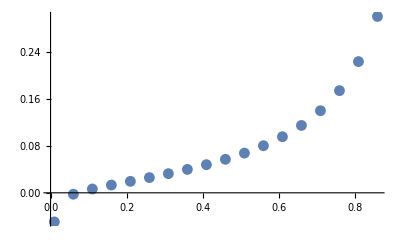

```mathematica
Block[{β1},ListPlot[Table[{β1,ReplaceRepeated[Normal[β2[β1]],solall[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]]},{β1,0.01,0.9,0.05}]]]
```

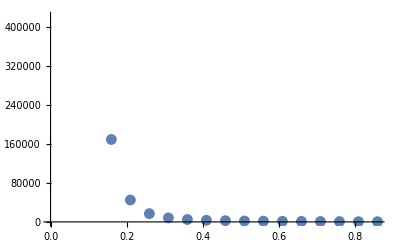

```mathematica
Block[{β1},ListPlot[Table[{β1,ReplaceRepeated[Normal[ω[β1]],solall[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]]},{β1,0.01,0.9,0.05}]]]
```

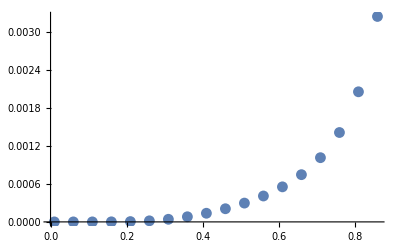

```mathematica
Block[{β1},ListPlot[Table[{β1,ReplaceRepeated[Normal[β2[β1]+β1]/Normal[ω[β1]],solall[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]]},{β1,0.01,0.9,0.05}]]]
```

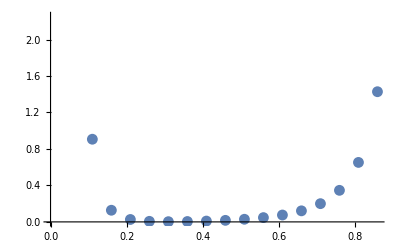

```mathematica
Block[{β1},ListPlot[Table[{β1,AngularMomentum[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]},{β1,0.01,0.9,0.05}]]]
```

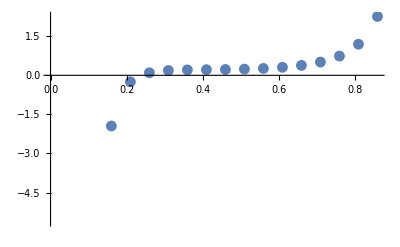

```mathematica
Block[{β1},ListPlot[Table[{β1,AngularMomentum[β1,150,150,0.9 10^-6,1/3,-1/3,-0.1]},{β1,0.01,0.9,0.05}]]]
```

```mathematica
Show[Plot[ReggeInterpolation[m1,m2,α,q1,q2,x1][Esq],{Esq,min,max}],ListPlot[Table[AngularMomentum[],Energy^2]]]
```

```mathematica
Int=ReggeInterpolation[150,150,0.9 10^-6,1/3,2/3,0.001]
```

InterpolatingFunction[{{335.581, 23457.9}}, <>]

```mathematica
Table[Flatten[{EE/.Solve[Int[EE]-JJ==0,EE],JJ}],{JJ,1,5}]
```

{{1177.94,1},{1597.25,2},{1922.99,3},{2199.23,4},{2443.48,5}}

```mathematica
Energy[0.99,150,150,0.9 10^-6,1/3,2/3,0.001]
```

23457.9

```mathematica
Int[7.97 10^3]
```

-2.9934

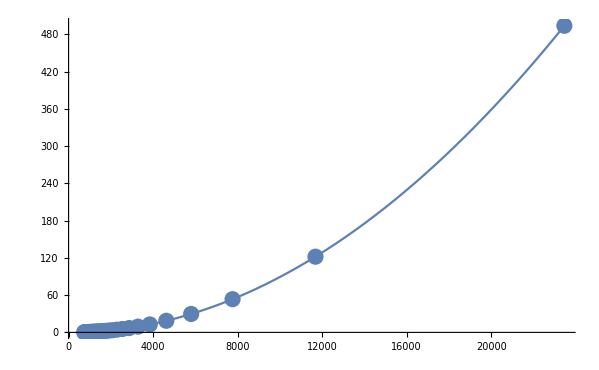

```mathematica
Block[{β1},Show[Plot[Int[E],{E,336,23500}],
ListPlot[Table[{Energy[β1,150,150,0.9 10^-6,1/3,2/3,0.001],AngularMomentum[β1,150,150,0.9 10^-6,1/3,2/3,0.001]},{β1,0.7,0.99,0.01}]]]]
```

### confront with data

```mathematica
PDGData={};
```

```mathematica
(*finds best fit of model*)
protonfit=NonlinearModelFit[data,{ReggeInterpolation[m1,m2,α,q1,q2,x1][Esq],x1<0&&m1>0&&m2>0&&α>0},{x1,m1,m2,α},Esq]
```

# perturbation analysis in α_e

### series definitions

z is the fine structure constant

```mathematica
β2[β1_]:=SeriesData[z,0,Table[y[β1,j],{j,1,2}],0,1,1];
Δθ[β1_] :=SeriesData[z,0,Table[th[β1,j],{j,1,2}],0,1,1];
ω[β1_] :=SeriesData[z,0,Table[w[β1,j],{j,1,2}],0,1,1];
```

### equations definitions

```mathematica
θeq[β1_]:=Δθ[β1]^2-β1^2-β2[β1]^2-2β1 β2[β1] Cos[Δθ[β1]];
eq1[β1_,m1_,m2_,α_,q1_,q2_,x_]:=1/(2π α) √(1-β1^2)-(m1 β1 ω[β1])/(√(1-β1^2))+(π x ω[β1]^2)/(2 (β1+β2[β1])^2)-(z q1 q2 ω[β1]^2 (β1+2 β1 β2[β1]^2+β1^3 β2[β1]^2+β2[β1] (1+β1^2 (2+β2[β1]^2)) Cos[Δθ[β1]]+(1+β1^2) β2[β1] Δθ[β1] Sin[Δθ[β1]]))/(Δθ[β1]+β1 β2[β1] Sin[Δθ[β1]])^3;
eq2[β1_,m1_,m2_,α_,q1_,q2_,x_]:=1/(2π α) √(1-β2[β1]^2)-(m2 β2[β1] ω[β1])/(√(1-β2[β1]^2))+(π x ω[β1]^2)/(2 (β1+β2[β1])^2)-(z q1 q2 ω[β1]^2 (β2[β1]+2 β1^2 β2[β1]+β1^2 β2[β1]^3+β1 (1+(2+β1^2) β2[β1]^2) Cos[Δθ[β1]]+β1 (1+β2[β1]^2) Δθ[β1] Sin[Δθ[β1]]))/(Δθ[β1]+β1 β2[β1] Sin[Δθ[β1]])^3;
H[β1_,m1_,m2_,α_,q1_,q2_,x_]:=1/ω[β1] 1/(2π α)(ArcSin[β1]+ArcSin[β2[β1]])+m1/(√(1-β1^2))+m2/(√(1-β2[β1]^2))+z q1 q2 ω[β1] (1/(β1 β2[β1] Sin[Δθ[β1]]+Δθ[β1]))-π/2(x ω[β1])/(β1+β2[β1]);
J[β1_,m1_,m2_,α_,q1_,q2_,x_]:=1/(2π α)(-β1 √(1-β1^2)+ArcSin[β1]-β2[β1] √(1-β2[β1]^2)+ArcSin[β2[β1]])/(2 ω[β1]^2)+m1 β1^2/(ω[β1] √(1-β1^2))+m2 β2[β1]^2/(ω[β1] √(1-β2[β1]^2))-2z q1 q2 β1 β2[β1] Cos[Δθ[β1]]/(β1 β2[β1] Sin[Δθ[β1]]+Δθ[β1]);
```

### handling ω and β_2

```mathematica
E11[β1_,m1_,m2_,α_,q1_,q2_,x_]:=SeriesCoefficient[eq1[β1,m1,m2,α,q1,q2,x],0];
E21[β1_,m1_,m2_,α_,q1_,q2_,x_]:=SeriesCoefficient[eq2[β1,m1,m2,α,q1,q2,x],0];
s0[β1_,m1_,m2_,α_,q1_,q2_,x_]:=Solve[E11[β1,m1,m2,α,q1,q2,x]==0&&E21[β1,m1,m2,α,q1,q2,x]==0,{w[β1,1],y[β1,1]}][[2]]//Simplify;
```

```mathematica
E12[β1_,m1_,m2_,α_,q1_,q2_,x_]:=SeriesCoefficient[eq1[β1,m1,m2,α,q1,q2,x],1]/.s0[β1,m1,m2,α,q1,q2,x]//Simplify;
E22[β1_,m1_,m2_,α_,q1_,q2_,x_]:=SeriesCoefficient[eq2[β1,m1,m2,α,q1,q2,x],1]/.s0[β1,m1,m2,α,q1,q2,x]//Simplify;
s1[β1_,m1_,m2_,α_,q1_,q2_,x_]:=Solve[E12[β1,m1,m2,α,q1,q2,x]==0&&E22[β1,m1,m2,α,q1,q2,x]==0,{w[β1,2],y[β1,2]}][[1]]//Simplify;
```

### handling Δθ

```mathematica
T1[β1_,m1_,m2_,α_,q1_,q2_,x_]:=SeriesCoefficient[θeq[β1],0]/.s0[β1,m1,m2,α,q1,q2,x]//Simplify;
T2[β1_,m1_,m2_,α_,q1_,q2_,x_]:=SeriesCoefficient[θeq[β1],1]/.s0[β1,m1,m2,α,q1,q2,x]//Simplify;
```

```mathematica
thsol2[β1_,m1_,m2_,α_,q1_,q2_,x_]:=Solve[T2[β1,m1,m2,α,q1,q2,x]==0,th[β1,2]][[1]];
```

```mathematica
thsol1[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x_]:=Solve[T1[β1,m1,m2,α,q1,q2,x]==0&&  0≤ th[β1,1],{th[β1,1]}][[1,1]];
```

```mathematica
(*ListPlot[Table[{r,thsol11[r,150,150,0.9 10^-6,1/3,-1/3][[2]]},{r,0.01,0.99,0.01}]]*)
```

### overall solution

```mathematica
solall[β1_,m1_,m2_,α_,q1_,q2_,x_]:=Flatten[{s0[β1,m1,m2,α,q1,q2,x],s1[β1,m1,m2,α,q1,q2,x],thsol1[β1,m1,m2,α,q1,q2,x],thsol2[β1,m1,m2,α,q1,q2,x]}];
AngularMomentum[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x_]:=ReplaceRepeated[Normal[J[β1,m1,m2,α,q1,q2,x]],solall[β1,m1,m2,α,q1,q2,x]];
Energy[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x_]:=ReplaceRepeated[Normal[H[β1,m1,m2,α,q1,q2,x]],solall[β1,m1,m2,α,q1,q2,x]];
vJ[J_,m1_,m2_,α_,q1_,q2_,x_]:=Block[{v},
v/.NSolve[AngularMomentum[v,m1,m2,α,q1,q2,x]==J&&0<v< 1,v]]
```

### Check error magnitude (in next order of pert.)

### generate regge points

```mathematica
PlotRegge[β1min_,β1max_,m1_,m2_,α_,q1_,q2_,x_]:=ListPlot[Evaluate[Table[ReplaceRepeated[Normal[{J[v,m1,m2,α,q1,q2,x],H[v,m1,m2,α,q1,q2,x]}],solall[v,m1,m2,α,q1,q2,x]]
,{v,β1min,β1max,(β1max-β1min)/10}]]]
```

```mathematica
point[j_,m1_,m2_,α_,q1_,q2_,x_,z1_]:=Block[{v},v=vJ[j,m1,m2,α,q1,q2,x]
ReplaceRepeated[Normal[{Energy[v,m1,m2,α,q1,q2,x]^2,j}],z->z1]]
```

# perturbation analysis in α

## definitions

### series definitions

x is the regge slope

```mathematica
β1=SeriesData[x,0,Table[b1[i],{i,1,2}],0,2,1];
β2=SeriesData[x,0,Table[b2[i],{i,1,2}],0,2,1];
Δθ=SeriesData[x,0,Table[th[i],{i,1,2}],0,2,1];
ω=SeriesData[x,0,Table[w[i],{i,1,2}],0,2,1];
```

### equations definitions

```mathematica
θeq=Δθ^2-β1^2-β2^2-2β1 β2 Cos[Δθ];
eq1[m1_,m2_,a_,z_,q1_,q2_]:=1/(2π x) √(1-β1^2)-(m1 β1 ω)/(√(1-β1^2))+(π a ω^2)/(2 (β1+β2)^2)-(z q1 q2 ω^2 (β1+2 β1 β2^2+β1^3 β2^2+β2 (1+β1^2 (2+β2^2)) Cos[Δθ]+(1+β1^2) β2 Δθ Sin[Δθ]))/(Δθ+β1 β2 Sin[Δθ])^3;
eq2[m1_,m2_,a_,z_,q1_,q2_]:=1/(2π x) √(1-β2^2)-(m2 β2 ω)/(√(1-β2^2))+(π a ω^2)/(2 (β1+β2)^2)-(z q1 q2 ω^2 (β2+2 β1^2 β2+β1^2 β2^3+β1 (1+(2+β1^2) β2^2) Cos[Δθ]+β1 (1+β2^2) Δθ Sin[Δθ]))/(Δθ+β1 β2 Sin[Δθ])^3;
H[m1_,m2_,a_,z_,q1_,q2_]:=1/ω 1/(2π x)(ArcSin[β1]+ArcSin[β2])+m1/(√(1-β1^2))+m2/(√(1-β2^2))+z q1 q2 ω (1/(β1 β2 Sin[Δθ]+Δθ))-π/2(a ω)/(β1+β2);
J[m1_,m2_,a_,z_,q1_,q2_]:=1/(2π x)(-β1 √(1-β1^2)+ArcSin-β2 √(1-β2^2)+ArcSin[β2])/(2 ω^2)+m1 β1^2/(ω √(1-β1^2))+m2 β2^2/(ω √(1-β2^2))-2z q1 q2 β1 β2 Cos[Δθ]/(β1 β2 Sin[Δθ]+Δθ);
```

### handling ω and β_2

```mathematica
E111[m1_,m2_,a_,z_,q1_,q2_]:=SeriesCoefficient[eq1[m1,m2,a,z,q1,q2],0];
E211[m1_,m2_,a_,z_,q1_,q2_]:=SeriesCoefficient[eq2[m1,m2,a,z,q1,q2],0];
(*s0[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[E111[β1,m1,m2,α,q1,q2]==0&&E211[β1,m1,m2,α,q1,q2]==0,{w[β1,1,1],y[β1,1,1]}][[2]]//Simplify;*)
```

```mathematica
eq1[m1,m2,a,z,q1,q2]
```

(√(1-b1[1]^2))/(2 π x)+(-(b1[1] b1[2])/(2 π √(1-b1[1]^2))-(m1 b1[1] w[1])/(√(1-b1[1]^2))+(a π w[1]^2)/(2 (b1[1]+b2[1])^2)-(q1 q2 z (b1[1]+2 b1[1] b2[1]^2+b1[1]^3 b2[1]^2+b2[1] (1+b1[1]^2 (2+b2[1]^2)) Cos[th[1]]+(1+b1[1]^2) b2[1] Sin[th[1]] th[1]) w[1]^2)/(b1[1] b2[1] Sin[th[1]]+th[1])^3)+O[x]^1

```mathematica
β1
```

b1[1]+b1[2] x+O[x]^2

```mathematica
E121[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq1[β1,m1,m2,α,q1,q2],{1,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
E221[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq2[β1,m1,m2,α,q1,q2],{1,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
E112[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq1[β1,m1,m2,α,q1,q2],{0,1}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
E212[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[eq2[β1,m1,m2,α,q1,q2],{0,1}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
s21[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[E121[β1,m1,m2,α,q1,q2]==0&&E221[β1,m1,m2,α,q1,q2]==0,{w[β1,2,1],y[β1,2,1]}][[1]]//Simplify;
s12[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[E112[β1,m1,m2,α,q1,q2]==0&&E212[β1,m1,m2,α,q1,q2]==0,{w[β1,1,2],y[β1,1,2]}][[1]]//Simplify;
```

### handling Δθ

```mathematica
T11[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[θeq[β1],{0,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
T12[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[θeq[β1],{0,1}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
T21[β1_,m1_,m2_,α_,q1_,q2_]:=SeriesCoefficient[θeq[β1],{1,0}]/.s0[β1,m1,m2,α,q1,q2]//Simplify;
```

```mathematica
thsol12[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[T12[β1,m1,m2,α,q1,q2]==0,th[β1,1,2]][[1]];
thsol21[β1_,m1_,m2_,α_,q1_,q2_]:=Solve[T21[β1,m1,m2,α,q1,q2]==0,th[β1,2,1]][[1]];
```

```mathematica
thsol11[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ]:=Solve[T11[β1,m1,m2,α,q1,q2]==0&&  0≤ th[β1,1,1],{th[β1,1,1]}][[1,1]];
```

```mathematica
(*ListPlot[Table[{r,thsol11[r,150,150,0.9 10^-6,1/3,-1/3][[2]]},{r,0.01,0.99,0.01}]]*)
```

### overall solution

```mathematica
solall[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=Flatten[{s0[β1,m1,m2,α,q1,q2],s12[β1,m1,m2,α,q1,q2],s21[β1,m1,m2,α,q1,q2],thsol11[β1,m1,m2,α,q1,q2],thsol12[β1,m1,m2,α,q1,q2],thsol21[β1,m1,m2,α,q1,q2],x->x1,z->1/137}];

solall[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=Flatten[{s0[β1,m1,m2,α,q1,q2],s12[β1,m1,m2,α,q1,q2],s21[β1,m1,m2,α,q1,q2],thsol12[β1,m1,m2,α,q1,q2],thsol21[β1,m1,m2,α,q1,q2],x->x1,z->1/137}];

AngularMomentum[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=ReplaceRepeated[Normal[J[β1,m1,m2,α,q1,q2]],solall[β1,m1,m2,α,q1,q2,x1]];
Energy[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=ReplaceRepeated[Normal[H[β1,m1,m2,α,q1,q2]],solall[β1,m1,m2,α,q1,q2,x1]];
(*approximately find velocity for given J*)
(*vJ[J_,m1_,m2_,α_,q1_,q2_,x1_]:=Block[{v,data,Jint},
data=Table[{v,AngularMomentum[v,m1,m2,α,q1,q2,x1]},{v,10^-5,1-10^-5,(1-2 10^-5)/5}];
Jint=Interpolation[data];
v=0.5;
While[Abs[J-Jint[v]]>10^-AccuracyGoal+Abs[J] 10^-PrecisionGoal
,]
v/.NSolve[==J&&0<v< 1,v]]*)
(*returns interpolation of trajectory*)
ReggeInterpolation[m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,x1_]:=Block[{β1},
Interpolation[DeleteCases[Table[{Energy[β1,m1,m2,α,q1,q2,x1],AngularMomentum[β1,m1,m2,α,q1,q2,x1]},{β1,0.01,0.99,0.02}],{E_,J_}/;J<0]]]
```

### Check error magnitude (in next order of pert.)

### generate regge points

```mathematica
PlotRegge[β1min_,β1max_,m1_,m2_,α_,q1_,q2_,x1_]:=ListPlot[Evaluate[Table[ReplaceRepeated[Normal[{J[v,m1,m2,α,q1,q2],H[v,m1,m2,α,q1,q2]}],solall[v,m1,m2,α,q1,q2,x1]]
,{v,β1min,β1max,(β1max-β1min)/10}]]]
```

```mathematica
point[j_,m1_,m2_,α_,q1_,q2_,x1_]:=Block[{v},v=vJ[j,m1,m2,α,q1,q2,x1]
ReplaceRepeated[Normal[{Energy[v,m1,m2,α,q1,q2]^2,j}],{z->1/137,x-> x1}]]
```

## calculations

```mathematica
ss=Simplify[Normal[β2[β1]]/.solall[β1,m1,m2,α,q1,q2,x1]];
```

```mathematica
ReplaceAll[ss,th[xx_,1,1]->xx]
```

(m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2))/(2 m1 β1)-(x1 (-1+β1^2)^2 (m2^3 √(2-2 β1^2) (-1+β1^2)^2+m2^2 √(2-2 β1^2) (-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-m1^2 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^2 m2 β1^2 (2 √(2-2 β1^2)+√(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))))/(√2 m1 α β1 (2 m1 β1^2+m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2))^2 (4 m1^2 β1^2+m2^2 (-1+β1^2)^2+m2 (-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))+(2 √2 q1 q2 (-1+β1^2)^2 (2 m1 m2^5 √(2-2 β1^2)+9 m1^3 m2^3 β1^2 √(2-2 β1^2)-7 m1 m2^5 β1^2 √(2-2 β1^2)+6 m1^5 m2 β1^4 √(2-2 β1^2)-14 m1^3 m2^3 β1^4 √(2-2 β1^2)+8 m1 m2^5 β1^4 √(2-2 β1^2)+2 m1^5 m2 β1^6 √(2-2 β1^2)+m1^3 m2^3 β1^6 √(2-2 β1^2)-2 m1 m2^5 β1^6 √(2-2 β1^2)+4 m1^3 m2^3 β1^8 √(2-2 β1^2)-2 m1 m2^5 β1^8 √(2-2 β1^2)+m1 m2^5 β1^10 √(2-2 β1^2)-2 m1 m2^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-5 m1^3 m2^2 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+5 m1 m2^4 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+3 m1^3 m2^2 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-3 m1 m2^4 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+2 m1^3 m2^2 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-m1 m2^4 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+m1 m2^4 β1^8 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)-m1^4 m2^2 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^4 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-2 m1^6 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-4 m1^4 m2^2 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+4 m1^2 m2^4 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-6 m1^6 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+11 m1^4 m2^2 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-6 m1^2 m2^4 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-6 m1^4 m2^2 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+4 m1^2 m2^4 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^4 β1^10 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^4 m2 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^2 m2^3 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+3 m1^4 m2 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-3 m1^2 m2^3 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-4 m1^4 m2 β1^6 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+3 m1^2 m2^3 β1^6 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^3 β1^8 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1^2 m2^4 √(2-2 β1^2) Cos[β1]-m2^6 √(2-2 β1^2) Cos[β1]-3 m1^4 m2^2 β1^2 √(2-2 β1^2) Cos[β1]-4 m1^2 m2^4 β1^2 √(2-2 β1^2) Cos[β1]+5 m2^6 β1^2 √(2-2 β1^2) Cos[β1]-8 m1^4 m2^2 β1^4 √(2-2 β1^2) Cos[β1]+18 m1^2 m2^4 β1^4 √(2-2 β1^2) Cos[β1]-10 m2^6 β1^4 √(2-2 β1^2) Cos[β1]+11 m1^4 m2^2 β1^6 √(2-2 β1^2) Cos[β1]-20 m1^2 m2^4 β1^6 √(2-2 β1^2) Cos[β1]+10 m2^6 β1^6 √(2-2 β1^2) Cos[β1]+7 m1^2 m2^4 β1^8 √(2-2 β1^2) Cos[β1]-5 m2^6 β1^8 √(2-2 β1^2) Cos[β1]+m2^6 β1^10 √(2-2 β1^2) Cos[β1]+m1^2 m2^3 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+m2^5 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+m1^4 m2 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+3 m1^2 m2^3 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]-4 m2^5 β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+3 m1^4 m2 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]-9 m1^2 m2^3 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+6 m2^5 β1^4 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+5 m1^2 m2^3 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]-4 m2^5 β1^6 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+m2^5 β1^8 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) Cos[β1]+2 m1^3 m2^3 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+7 m1^5 m2 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-5 m1^3 m2^3 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-4 m1^5 m2 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+3 m1^3 m2^3 β1^6 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-3 m1^5 m2 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+m1^3 m2^3 β1^8 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-m1^3 m2^3 β1^10 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-2 m1^3 m2^2 β1^2 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-3 m1^5 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+3 m1^3 m2^2 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-m1^5 β1^6 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]-m1^3 m2^2 β1^8 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)) Cos[β1]+m1^2 β1 (m2^4 √(2-2 β1^2) (-1+β1^2)^3 (1+β1^2)-2 m1^3 β1^4 √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))+m1^2 m2 β1^2 (√(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+4 m1 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-4 m1 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))+m2^3 (-1+β1^2)^2 (√(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+β1^2 √(2-2 β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)+m1 β1^2 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2))-m1 β1^4 √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))-m1 m2^2 β1^2 (-1+β1^2) (-3 m1 √(2-2 β1^2) (1+β1^2)+(-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2) √(-(m2 (-1+β1^2) (m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)))/(m1^2 β1^2)))) Sin[β1]))/(137 m1^3 π α β1^4 (4 m1^2 β1^2+m2^2 (-1+β1^2)^2+m2 (-1+β1^2) √(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)) (2 m1 β1+(m2 (-1+β1^2)+√(4 m1^2 β1^2+m2^2 (-1+β1^2)^2)) Sin[β1])^3)

```mathematica
Simplify[Series[ReplaceAll[ss,{th[xx_,1,1]->xx,x1->0}],{β1,0.5,3}],m1>0&&m2>0&&α>0]
```

((1. (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1-(0.0213308 (m2^5 (0.707213 m2-0.942951 √(1. m1^2+0.5625 m2^2))+m1^2 (3.88677 m2^4-4.34418 m2^3 √(1. m1^2+0.5625 m2^2)-1.12157 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))))+m1 (-2.4176 m2^5+3.22346 m2^4 √(1. m1^2+0.5625 m2^2)+0.379889 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))-0.506518 m2^(7/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))))+m1^5 (-1.37959 m2+1.05056 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+1. √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2))+m1^4 (3.78539 m2^2-1.55822 m2 √(1. m1^2+0.5625 m2^2)-1.74695 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))-1.80095 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2))+m1^3 (-4.7755 m2^3+1.68839 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+m2^2 (3.50203 √(1. m1^2+0.5625 m2^2)+1.49543 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)))) q1 q2)/(m1^3 (1. m1-0.359569 m2+0.479426 √(1. m1^2+0.5625 m2^2))^3 (1. m1^2+0.5625 m2^2-0.75 m2 √(1. m1^2+0.5625 m2^2)) α))+(198.411 (m2^10 (-0.040451 m2+0.0539346 √(1. m1^2+0.5625 m2^2)) q1 q2+m1 (0.190629 m2^10-0.254171 m2^9 √(1. m1^2+0.5625 m2^2)-0.0177098 √(m2^19 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.023613 m2^(17/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))) q1 q2+1.03114 m1^12 m2 α+m1^11 m2 (-4.03034 m2+1. √(1. m1^2+0.5625 m2^2)) α+m1^10 (-0.116607 m2 q1 q2+(0.078274 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.0763625 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+8.81169 m2^3 α-4.03772 m2^2 √(1. m1^2+0.5625 m2^2) α)+m1^9 (0.539205 m2^2 q1 q2-0.120974 m2 √(1. m1^2+0.5625 m2^2) q1 q2-0.281821 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-0.28539 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2) q1 q2-13.543 m2^4 α+8.57402 m2^3 √(1. m1^2+0.5625 m2^2) α)+m1^8 (-1.26704 m2^3 q1 q2+0.57156 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.52705 m2^2 (1. √(1. m1^2+0.5625 m2^2)+1.04416 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+15.7183 m2^5 α-12.3522 m2^4 √(1. m1^2+0.5625 m2^2) α)+m1^7 (2.07864 m2^4 q1 q2-0.801747 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.24376 m2^3 (1. √(1. m1^2+0.5625 m2^2)+0.575121 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-14.3972 m2^6 α+13.3535 m2^5 √(1. m1^2+0.5625 m2^2) α)+m1^6 (-2.56975 m2^5 q1 q2+0.836099 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+1.93561 m2^4 (1. √(1. m1^2+0.5625 m2^2)+0.357144 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+10.5878 m2^7 α-11.1315 m2^6 √(1. m1^2+0.5625 m2^2) α)+m1^5 (2.45357 m2^6 q1 q2-0.687142 √(m2^11 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-2.20283 m2^5 (1. √(1. m1^2+0.5625 m2^2)+0.225176 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-6.12727 m2^8 α+7.10529 m2^7 √(1. m1^2+0.5625 m2^2) α)+m1^4 (-1.89204 m2^7 q1 q2+0.441914 √(m2^13 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+1.95185 m2^6 (1. √(1. m1^2+0.5625 m2^2)+0.135004 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+2.73441 m2^9 α-3.45452 m2^8 √(1. m1^2+0.5625 m2^2) α)+m1^3 (1.1558 m2^8 q1 q2-0.213373 √(m2^15 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.31514 m2^7 (1. √(1. m1^2+0.5625 m2^2)+0.0797223 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.898094 m2^10 α+1.19746 m2^9 √(1. m1^2+0.5625 m2^2) α)+m1^2 (-0.535603 m2^9 q1 q2+0.666196 m2^8 √(1. m1^2+0.5625 m2^2) q1 q2+0.0786342 √(m2^17 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.161464 m2^11 α-0.215285 m2^10 √(1. m1^2+0.5625 m2^2) α)) (β1-0.5))/(m1^3 √(1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)) (2.08583 m1-0.75 m2+1. √(1. m1^2+0.5625 m2^2))^4 (-1.33333 m1^2+m2 (-0.75 m2+1. √(1. m1^2+0.5625 m2^2)))^2 α)+(1333.65 (m2^26 (-0.00589622 m2+0.00786162 √(1. m1^2+0.5625 m2^2)) q1 q2+m1 (0.0356805 m2^26-0.047574 m2^25 √(1. m1^2+0.5625 m2^2)-0.00215476 √(m2^51 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.00287302 m2^(49/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))) q1 q2+0.989269 m1^28 m2 α+m1^27 m2 (-6.47143 m2+1. √(1. m1^2+0.5625 m2^2)) α+m1^26 (-0.584628 m2 q1 q2+(0.350825 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.354322 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+24.5916 m2^3 α-6.45182 m2^2 √(1. m1^2+0.5625 m2^2) α)+m1^25 (3.78322 m2^2 q1 q2-0.577758 m2 √(1. m1^2+0.5625 m2^2) q1 q2-1.99425 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.9841 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2) q1 q2-68.8384 m2^4 α+24.3373 m2^3 √(1. m1^2+0.5625 m2^2) α)+m1^24 (-14.837 m2^3 q1 q2+7.07314 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+3.8102 m2^2 (1. √(1. m1^2+0.5625 m2^2)+1.83523 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+154.631 m2^5 α-67.0122 m2^4 √(1. m1^2+0.5625 m2^2) α)+m1^23 (42.3059 m2^4 q1 q2-18.6805 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-14.6116 m2^3 (1. √(1. m1^2+0.5625 m2^2)+1.23875 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-292.531 m2^6 α+147.797 m2^5 √(1. m1^2+0.5625 m2^2) α)+m1^22 (-97.4997 m2^5 q1 q2+39.9492 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+41.3341 m2^4 (1. √(1. m1^2+0.5625 m2^2)+0.919527 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+479.764 m2^7 α-274.008 m2^6 √(1. m1^2+0.5625 m2^2) α)+m1^21 (188.828 m2^6 q1 q2-72.3633 √(m2^11 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-93.3073 m2^5 (1. √(1. m1^2+0.5625 m2^2)+0.721975 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-694.627 m2^8 α+439.06 m2^7 √(1. m1^2+0.5625 m2^2) α)+m1^20 (-317.258 m2^7 q1 q2+114.064 √(m2^13 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+177.407 m2^6 (1. √(1. m1^2+0.5625 m2^2)+0.583971 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+899.906 m2^9 α-620.194 m2^8 √(1. m1^2+0.5625 m2^2) α)+m1^19 (470.961 m2^8 q1 q2-159.061 √(m2^15 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-291.643 m2^7 (1. √(1. m1^2+0.5625 m2^2)+0.48303 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-1052.78 m2^10 α+782.015 m2^9 √(1. m1^2+0.5625 m2^2) α)+m1^18 (-625.285 m2^9 q1 q2+198.947 √(m2^17 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+422.477 m2^8 (1. √(1. m1^2+0.5625 m2^2)+0.405184 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+1119.46 m2^11 α-888.384 m2^10 √(1. m1^2+0.5625 m2^2) α)+m1^17 (750.537 m2^10 q1 q2-224.847 √(m2^19 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-547.044 m2^9 (1. √(1. m1^2+0.5625 m2^2)+0.343149 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-1087.5 m2^12 α+915.452 m2^11 √(1. m1^2+0.5625 m2^2) α)+m1^16 (-818.91 m2^11 q1 q2+231.212 √(m2^21 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+638.059 m2^10 (1. √(1. m1^2+0.5625 m2^2)+0.292754 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+968.012 m2^13 α-859.286 m2^12 √(1. m1^2+0.5625 m2^2) α)+m1^15 (816.849 m2^12 q1 q2-217.274 √(m2^23 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-675.714 m2^11 (1. √(1. m1^2+0.5625 m2^2)+0.250564 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-791.291 m2^14 α+737.15 m2^13 √(1. m1^2+0.5625 m2^2) α)+m1^14 (-747.313 m2^13 q1 q2+186.991 √(m2^25 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+652.339 m2^12 (1. √(1. m1^2+0.5625 m2^2)+0.215038 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+594.626 m2^15 α-578.87 m2^14 √(1. m1^2+0.5625 m2^2) α)+m1^13 (628.076 m2^14 q1 q2-147.795 √(m2^27 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-575.827 m2^13 (1. √(1. m1^2+0.5625 m2^2)+0.18447 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-410.605 m2^16 α+416.24 m2^15 √(1. m1^2+0.5625 m2^2) α)+m1^12 (-485.96 m2^15 q1 q2+107.2 √(m2^29 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+465.988 m2^14 (1. √(1. m1^2+0.5625 m2^2)+0.15794 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+260.392 m2^17 α-274.014 m2^16 √(1. m1^2+0.5625 m2^2) α)+m1^11 (345.74 m2^16 q1 q2-71.3691 √(m2^31 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-345.489 m2^15 (1. √(1. m1^2+0.5625 m2^2)+0.134802 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-151.236 m2^18 α+164.732 m2^17 √(1. m1^2+0.5625 m2^2) α)+m1^10 (-226.178 m2^17 q1 q2+234.86 m2^16 √(1. m1^2+0.5625 m2^2) q1 q2+43.5409 √(m2^33 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+80.1746 m2^19 α-90.1853 m2^18 √(1. m1^2+0.5625 m2^2) α)+m1^9 (135.754 m2^18 q1 q2-24.2258 √(m2^35 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+26.8174 m2^(33/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-146.033 m2^17 (1. √(1. m1^2+0.5625 m2^2)+0.0960601 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-38.6187 m2^20 α+44.749 m2^19 √(1. m1^2+0.5625 m2^2) α)+m1^8 (-74.4089 m2^19 q1 q2+12.2764 √(m2^37 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+82.752 m2^18 (1. √(1. m1^2+0.5625 m2^2)+0.0796451 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+16.7476 m2^21 α-19.9529 m2^20 √(1. m1^2+0.5625 m2^2) α)+m1^7 (37.1768 m2^20 q1 q2-5.60053 √(m2^39 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-42.6383 m2^19 (1. √(1. m1^2+0.5625 m2^2)+0.064968 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-6.49231 m2^22 α+7.93733 m2^21 √(1. m1^2+0.5625 m2^2) α)+m1^6 (-16.7317 m2^21 q1 q2+2.28804 √(m2^41 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+19.7499 m2^20 (1. √(1. m1^2+0.5625 m2^2)+0.051846 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+2.2085 m2^23 α-2.76375 m2^22 √(1. m1^2+0.5625 m2^2) α)+m1^5 (6.75185 m2^22 q1 q2-0.825508 √(m2^43 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-8.19259 m2^21 (1. √(1. m1^2+0.5625 m2^2)+0.0394463 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.644814 m2^24 α+0.825893 m2^23 √(1. m1^2+0.5625 m2^2) α)+m1^4 (-2.40294 m2^23 q1 q2+0.253631 √(m2^45 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+2.98618 m2^22 (1. √(1. m1^2+0.5625 m2^2)+0.0293327 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+0.158129 m2^25 α-0.205969 m2^24 √(1. m1^2+0.5625 m2^2) α)+m1^3 (0.730909 m2^24 q1 q2-0.06761 √(m2^47 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-0.932258 m2^23 (1. √(1. m1^2+0.5625 m2^2)+0.0181093 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.0285683 m2^26 α+0.038091 m2^25 √(1. m1^2+0.5625 m2^2) α)+m1^2 (-0.191576 m2^25 q1 q2+0.248447 m2^24 √(1. m1^2+0.5625 m2^2) q1 q2+0.0126619 √(m2^49 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.00410891 m2^27 α-0.00547855 m2^26 √(1. m1^2+0.5625 m2^2) α)) (β1-0.5)^2)/(m1^3 (1. m1^2+0.5625 m2^2)^(13/2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))^2 (2.08583 m1-0.75 m2+1. √(1. m1^2+0.5625 m2^2))^5 (-1.33333 m1^2+m2 (-0.75 m2+1. √(1. m1^2+0.5625 m2^2)))^3 α)+(42.0187 (m2^39 (0.0011943 m2-0.00159239 √(1. m1^2+0.5625 m2^2)) q1 q2+m1 (-0.00885375 m2^39+0.011805 m2^38 √(1. m1^2+0.5625 m2^2)+0.000374124 √(m2^77 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))-0.000498832 m2^(75/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))) q1 q2+0.996211 m1^41 m2 α+m1^40 m2 (-8.69766 m2+1. √(1. m1^2+0.5625 m2^2)) α+m1^39 (-1.68707 m2 q1 q2+(0.955057 √(m2 (-0.75 m2+√(1. m1^2+0.5625 m2^2)))+0.958529 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+43.5031 m2^3 α-8.6859 m2^2 √(1. m1^2+0.5625 m2^2) α)+m1^38 (14.4591 m2^2 q1 q2-1.68033 m2 √(1. m1^2+0.5625 m2^2) q1 q2-7.31387 √(m2^3 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-7.30003 m2 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2) q1 q2-159.336 m2^4 α+43.2489 m2^3 √(1. m1^2+0.5625 m2^2) α)+m1^37 (-73.6232 m2^3 q1 q2+34.3677 √(m2^5 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+14.4932 m2^2 (1. √(1. m1^2+0.5625 m2^2)+2.35541 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+468.796 m2^5 α-156.852 m2^4 √(1. m1^2+0.5625 m2^2) α)+m1^36 (274.361 m2^4 q1 q2-119.926 √(m2^7 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-73.0414 m2^3 (1. √(1. m1^2+0.5625 m2^2)+1.61273 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-1166.07 m2^6 α+456.709 m2^5 √(1. m1^2+0.5625 m2^2) α)+m1^35 (-826.447 m2^5 q1 q2+339.933 √(m2^9 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+270.536 m2^4 (1. √(1. m1^2+0.5625 m2^2)+1.22159 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+2527.62 m2^7 α-1122.3 m2^6 √(1. m1^2+0.5625 m2^2) α)+m1^34 (2105.42 m2^6 q1 q2-820.229 √(m2^11 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-805.527 m2^5 (1. √(1. m1^2+0.5625 m2^2)+0.977329 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-4873.6 m2^8 α+2400.81 m2^7 √(1. m1^2+0.5625 m2^2) α)+m1^33 (-4683.29 m2^7 q1 q2+1732.74 √(m2^13 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+2030.52 m2^6 (1. √(1. m1^2+0.5625 m2^2)+0.808264 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+8481.94 m2^9 α-4564.2 m2^8 √(1. m1^2+0.5625 m2^2) α)+m1^32 (9272.01 m2^8 q1 q2-3267.78 √(m2^15 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-4459. m2^7 (1. √(1. m1^2+0.5625 m2^2)+0.684235 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-13467.5 m2^10 α+7824.13 m2^9 √(1. m1^2+0.5625 m2^2) α)+m1^31 (-16580.5 m2^9 q1 q2+5577.44 √(m2^17 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+8711.78 m2^8 (1. √(1. m1^2+0.5625 m2^2)+0.588663 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+19671. m2^11 α-12226.7 m2^10 √(1. m1^2+0.5625 m2^2) α)+m1^30 (27064.6 m2^10 q1 q2-8702.34 √(m2^19 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-15357.8 m2^9 (1. √(1. m1^2+0.5625 m2^2)+0.512737 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-26600.4 m2^12 α+17560.5 m2^11 √(1. m1^2+0.5625 m2^2) α)+m1^29 (-40650.5 m2^11 q1 q2+12511.2 √(m2^21 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+24690.6 m2^10 (1. √(1. m1^2+0.5625 m2^2)+0.450769 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+33472.2 m2^13 α-23330.2 m2^12 √(1. m1^2+0.5625 m2^2) α)+m1^28 (56546.6 m2^12 q1 q2-16671.7 √(m2^23 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-36500.6 m2^11 (1. √(1. m1^2+0.5625 m2^2)+0.399162 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-39354.6 m2^14 α+28818. m2^13 √(1. m1^2+0.5625 m2^2) α)+m1^27 (-73204.6 m2^13 q1 q2+20691.8 √(m2^25 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+49923.4 m2^12 (1. √(1. m1^2+0.5625 m2^2)+0.355492 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+43375. m2^15 α-33229.6 m2^14 √(1. m1^2+0.5625 m2^2) α)+m1^26 (88562.8 m2^14 q1 q2-24010.1 √(m2^27 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-63501.1 m2^13 (1. √(1. m1^2+0.5625 m2^2)+0.317987 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-44934.2 m2^16 α+35886.3 m2^15 √(1. m1^2+0.5625 m2^2) α)+m1^25 (-100444. m2^15 q1 q2+26126.4 √(m2^29 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+75408.6 m2^14 (1. √(1. m1^2+0.5625 m2^2)+0.285438 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+43845.7 m2^17 α-36391.3 m2^16 √(1. m1^2+0.5625 m2^2) α)+m1^24 (107074. m2^16 q1 q2-26725.8 √(m2^31 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-83872.8 m2^15 (1. √(1. m1^2+0.5625 m2^2)+0.256883 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-40365.8 m2^18 α+34724.2 m2^17 √(1. m1^2+0.5625 m2^2) α)+m1^23 (-107509. m2^17 q1 q2+25747.8 √(m2^33 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+87598.2 m2^16 (1. √(1. m1^2+0.5625 m2^2)+0.231629 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+35107.5 m2^19 α-31227.1 m2^18 √(1. m1^2+0.5625 m2^2) α)+m1^22 (101830. m2^18 q1 q2-23397.6 √(m2^35 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-86076.5 m2^17 (1. √(1. m1^2+0.5625 m2^2)+0.209127 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-28872.1 m2^20 α+26497.9 m2^19 √(1. m1^2+0.5625 m2^2) α)+m1^21 (-91104.6 m2^19 q1 q2+20075.5 √(m2^37 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+79706.4 m2^18 (1. √(1. m1^2+0.5625 m2^2)+0.188934 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+22465.8 m2^21 α-21234.4 m2^20 √(1. m1^2+0.5625 m2^2) α)+m1^20 (77053.5 m2^20 q1 q2-16275.4 √(m2^39 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-69627.3 m2^19 (1. √(1. m1^2+0.5625 m2^2)+0.170724 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-16544.4 m2^22 α+16077.6 m2^21 √(1. m1^2+0.5625 m2^2) α)+m1^19 (-61641.5 m2^21 q1 q2+12472.2 √(m2^41 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+57424.1 m2^20 (1. √(1. m1^2+0.5625 m2^2)+0.154197 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+11530.7 m2^23 α-11503.2 m2^22 √(1. m1^2+0.5625 m2^2) α)+m1^18 (46654.9 m2^22 q1 q2-9033.92 √(m2^43 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-44732.1 m2^21 (1. √(1. m1^2+0.5625 m2^2)+0.139143 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-7603.33 m2^24 α+7776.17 m2^23 √(1. m1^2+0.5625 m2^2) α)+m1^17 (-33403.6 m2^23 q1 q2+6183.87 √(m2^45 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+32912.9 m2^22 (1. √(1. m1^2+0.5625 m2^2)+0.125362 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+4740.11 m2^25 α-4963.74 m2^24 √(1. m1^2+0.5625 m2^2) α)+m1^16 (22617.6 m2^24 q1 q2-3997.32 √(m2^47 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-22870.3 m2^23 (1. √(1. m1^2+0.5625 m2^2)+0.112699 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-2791.2 m2^26 α+2989.37 m2^25 √(1. m1^2+0.5625 m2^2) α)+m1^15 (-14470.6 m2^25 q1 q2+2437.82 √(m2^49 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+14997.4 m2^24 (1. √(1. m1^2+0.5625 m2^2)+0.101034 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+1550.16 m2^27 α-1696.2 m2^26 √(1. m1^2+0.5625 m2^2) α)+m1^14 (8739.72 m2^26 q1 q2-1400.78 √(m2^51 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-9273.36 m2^25 (1. √(1. m1^2+0.5625 m2^2)+0.0902291 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-810.46 m2^28 α+905.192 m2^27 √(1. m1^2+0.5625 m2^2) α)+m1^13 (-4975.54 m2^27 q1 q2+756.793 √(m2^53 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+5398.99 m2^26 (1. √(1. m1^2+0.5625 m2^2)+0.0802284 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+397.953 m2^29 α-453.271 m2^28 √(1. m1^2+0.5625 m2^2) α)+m1^12 (2664.52 m2^28 q1 q2-383.687 √(m2^55 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-2954.03 m2^27 (1. √(1. m1^2+0.5625 m2^2)+0.070906 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-182.915 m2^30 α+212.3 m2^29 √(1. m1^2+0.5625 m2^2) α)+m1^11 (-1339.49 m2^29 q1 q2+181.87 √(m2^57 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+1515.78 m2^28 (1. √(1. m1^2+0.5625 m2^2)+0.0622347 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+78.4198 m2^31 α-92.6761 m2^30 √(1. m1^2+0.5625 m2^2) α)+m1^10 (629.783 m2^30 q1 q2-726.814 m2^29 √(1. m1^2+0.5625 m2^2) q1 q2-80.3544 √(m2^59 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-31.1875 m2^32 α+37.5011 m2^31 √(1. m1^2+0.5625 m2^2) α)+m1^9 (-276.079 m2^31 q1 q2+32.9098 √(m2^61 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-39.3445 m2^(59/2) √((1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+324.681 m2^30 (1. √(1. m1^2+0.5625 m2^2)+0.0465268 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+11.4366 m2^33 α-13.9837 m2^32 √(1. m1^2+0.5625 m2^2) α)+m1^8 (112.205 m2^32 q1 q2-12.4132 √(m2^63 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-134.347 m2^31 (1. √(1. m1^2+0.5625 m2^2)+0.0394803 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-3.83463 m2^34 α+4.76347 m2^33 √(1. m1^2+0.5625 m2^2) α)+m1^7 (-42.015 m2^33 q1 q2+4.28793 √(m2^65 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+51.1941 m2^32 (1. √(1. m1^2+0.5625 m2^2)+0.0327108 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+1.16033 m2^35 α-1.46411 m2^34 √(1. m1^2+0.5625 m2^2) α)+m1^6 (14.4041 m2^34 q1 q2-1.33126 √(m2^67 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-17.8364 m2^33 (1. √(1. m1^2+0.5625 m2^2)+0.0266591 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.313708 m2^36 α+0.401406 m2^35 √(1. m1^2+0.5625 m2^2) α)+m1^5 (-4.44213 m2^35 q1 q2+0.37279 √(m2^69 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+5.59219 m2^34 (1. √(1. m1^2+0.5625 m2^2)+0.0204894 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+0.0728527 m2^37 α-0.0946258 m2^36 √(1. m1^2+0.5625 m2^2) α)+m1^4 (1.23396 m2^36 q1 q2-0.0883597 √(m2^71 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-1.57502 m2^35 (1. √(1. m1^2+0.5625 m2^2)+0.0155342 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2-0.0145737 m2^38 α+0.0191306 m2^37 √(1. m1^2+0.5625 m2^2) α)+m1^3 (-0.290794 m2^37 q1 q2+0.0186826 √(m2^73 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2+0.377231 m2^36 (1. √(1. m1^2+0.5625 m2^2)+0.00963965 √((m2 (1. m1^2+0.5625 m2^2) (-0.75 m2+√(1. m1^2+0.5625 m2^2)))/m1^2)) q1 q2+0.00211881 m2^39 α-0.00282508 m2^38 √(1. m1^2+0.5625 m2^2) α)+m1^2 (0.0608736 m2^38 q1 q2-0.0797494 m2^37 √(1. m1^2+0.5625 m2^2) q1 q2-0.00272728 √(m2^75 (-0.75 m2+√(1. m1^2+0.5625 m2^2))) q1 q2-0.000253953 m2^40 α+0.000338604 m2^39 √(1. m1^2+0.5625 m2^2) α)) (β1-0.5)^3)/(m1^3 (1. m1^2+0.5625 m2^2)^11 (1. m1-0.359569 m2+0.479426 √(1. m1^2+0.5625 m2^2))^6 (-0.75 m2+√(1. m1^2+0.5625 m2^2))^3 (1. m1^2+0.5625 m2^2-0.75 m2 √(1. m1^2+0.5625 m2^2))^4 α)+O[β1-0.5]^4

### generate regge electromagnetic free trajectories at limits

```mathematica
solallneutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=Flatten[{s0[β1,m1,m2,α,q1,q2],s21[β1,m1,m2,α,q1,q2],x->x1,z->0}];
AngularMomentumneutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=ReplaceRepeated[Normal[J[β1,m1,m2,α,q1,q2]],solallneutral[β1,m1,m2,α,q1,q2,x1]];
Energyneutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=ReplaceRepeated[Normal[H[β1,m1,m2,α,q1,q2]],solallneutral[β1,m1,m2,α,q1,q2,x1]];
β2neutral[β1_,m1_,m2_,α_,q1_,q2_,x1_]:=ReplaceRepeated[Normal[β2[β1]],solallneutral[β1,m1,m2,α,q1,q2,x1]];
```

#### β -> 0

```mathematica
NonRelativisticRegge=ComposeSeries[Series[AngularMomentumneutral[β1,150,150,0.9 10^-6,0,0,a],{β1,0,3}],InverseSeries[Series[Energyneutral[β1,150,150,0.9 10^-6,0,0,a],{β1,0,3}],En]]
```

-(0.018251 a √En)/(√-a)+(-(0.018251 (-150.-617.284 a) a)/(√-a)-22.5321 √-a a) √(1/En)+(-79691. (0.254469-0.418879 a) √-a a-13908.7 √-a a (0.243+1. a)-(0.018251 a (-11250.+324074. a-76207.9 a^2))/(√-a)) (1/En)^(3/2)+O[1/En]^2

### graphs of quantities

```mathematica
Block[{β1},ListPlot[Table[{β1,ReplaceRepeated[Normal[β2[β1]],solall[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]]},{β1,0.01,0.9,0.05}]]]
```

-Graphics-

```mathematica
Block[{β1},ListPlot[Table[{β1,ReplaceRepeated[Normal[ω[β1]],solall[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]]},{β1,0.01,0.9,0.05}]]]
```

-Graphics-

```mathematica
Block[{β1},ListPlot[Table[{β1,ReplaceRepeated[Normal[β2[β1]+β1]/Normal[ω[β1]],solall[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]]},{β1,0.01,0.9,0.05}]]]
```

-Graphics-

```mathematica
Block[{β1},ListPlot[Table[{β1,AngularMomentum[β1,150,1500,0.9 10^-6,1/3,-1/3,0.001]},{β1,0.01,0.9,0.05}]]]
```

-Graphics-

```mathematica
Block[{β1},ListPlot[Table[{β1,AngularMomentum[β1,150,150,0.9 10^-6,1/3,-1/3,-0.1]},{β1,0.01,0.9,0.05}]]]
```

-Graphics-

```mathematica
Show[Plot[ReggeInterpolation[m1,m2,α,q1,q2,x1][Esq],{Esq,min,max}],ListPlot[Table[AngularMomentum[],Energy^2]]]
```

```mathematica
Int=ReggeInterpolation[150,150,0.9 10^-6,1/3,2/3,0.001]
```

InterpolatingFunction[{{335.581, 23457.9}}, <>]

```mathematica
Table[Flatten[{EE/.Solve[Int[EE]-JJ==0,EE],JJ}],{JJ,1,5}]
```

{{1177.94,1},{1597.25,2},{1922.99,3},{2199.23,4},{2443.48,5}}

```mathematica
Energy[0.99,150,150,0.9 10^-6,1/3,2/3,0.001]
```

23457.9

```mathematica
Int[7.97 10^3]
```

-2.9934

```mathematica
Block[{β1},Show[Plot[Int[E],{E,336,23500}],
ListPlot[Table[{Energy[β1,150,150,0.9 10^-6,1/3,2/3,0.001],AngularMomentum[β1,150,150,0.9 10^-6,1/3,2/3,0.001]},{β1,0.7,0.99,0.01}]]]]
```

-Graphics-

### confront with data

```mathematica
PDGData={};
```

```mathematica
(*finds best fit of model*)
protonfit=NonlinearModelFit[data,{ReggeInterpolation[m1,m2,α,q1,q2,x1][Esq],x1<0&&m1>0&&m2>0&&α>0},{x1,m1,m2,α},Esq]
```

# perturbation analysis in m1/m2

## all definitions and solution

### data and data manipulation

The object “particles” is a database of PDG data.

```mathematica
Clear[particles];
particles={
<|"type"-> "Meson","Name"-> "D_s^±","quarkContent"-> {"charm","strange"},"J"->0 ,"P"-> -1,"Spin"-> None,"Mass"-> 1968.3 MeV, "MassUncertainty"-> 0.1 MeV |>,
<|"type"-> "Meson","Name"-> "D_s^(*±)","quarkContent"-> {"charm","strange"},"J"->1 ,"P"-> -1,"Spin"-> None,"Mass"-> 2112.1 MeV, "MassUncertainty"-> 0.4 MeV |>,
<|"type"-> "Meson","Name"-> "D_s0^*(2317)^±","quarkContent"-> {"charm","strange"},"J"->0 ,"P"-> 1,"Spin"-> None,"Mass"-> 2317.7 MeV, "MassUncertainty"-> 0.6 MeV |>,
<|"type"-> "Meson","Name"-> "D_s1(2460)^±","quarkContent"-> {"charm","strange"},"J"->1 ,"P"-> 1,"Spin"-> None,"Mass"-> 2459.5 MeV, "MassUncertainty"-> 0.6 MeV |>,
<|"type"-> "Meson","Name"-> "D_s1(2536)^±","quarkContent"-> {"charm","strange"},"J"->1 ,"P"-> 1,"Spin"-> None,"Mass"-> 2535.11 MeV, "MassUncertainty"-> 0.06 MeV |>,
<|"type"-> "Meson","Name"-> "D_s2^*(2573)","quarkContent"-> {"charm","strange"},"J"->2 ,"P"-> 1,"Spin"-> None,"Mass"-> 2571.9 MeV, "MassUncertainty"-> 0.8MeV |>,
<|"type"-> "Meson","Name"-> "D_s1^*(2700)^±","quarkContent"-> {"charm","strange"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 2709 MeV, "MassUncertainty"-> 4MeV |>,
<|"type"-> "Meson","Name"-> "D_sJ^*(2860)^±","quarkContent"-> {"charm","strange"},"J"->3 ,"P"->-1,"Spin"-> None,"Mass"-> 2863.2 MeV, "MassUncertainty"-> 4MeV |>,
<|"type"-> "Meson","Name"-> "D_sJ(3040)^±","quarkContent"-> {"charm","strange"},"J"->None ,"P"->None,"Spin"-> None,"Mass"-> 3044 MeV, "MassUncertainty"-> 31MeV |>,

<|"type"-> "Meson","Name"-> "D^±","quarkContent"-> {"charm","down"},"J"->0 ,"P"->-1,"Spin"-> None,"Mass"-> 1869.61 MeV, "MassUncertainty"-> 0.09MeV |>,
<|"type"-> "Meson","Name"-> "D^0","quarkContent"-> {"charm","up"},"J"->0 ,"P"->-1,"Spin"-> None,"Mass"-> 1864.84 MeV, "MassUncertainty"-> 0.05MeV |>,
<|"type"-> "Meson","Name"-> "D^*(2007)^0","quarkContent"-> {"charm","up"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 2006.97 MeV, "MassUncertainty"-> 0.08MeV |>,
<|"type"-> "Meson","Name"-> "D^*(2010)^±","quarkContent"-> {"charm","down"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 2010.27MeV, "MassUncertainty"-> 0.05MeV |>,
<|"type"-> "Meson","Name"-> "D_0^*(2400)^0","quarkContent"-> {"charm","up"},"J"->0 ,"P"->1,"Spin"-> None,"Mass"-> 2318MeV, "MassUncertainty"-> 29MeV |>,
<|"type"-> "Meson","Name"-> "D_0^*(2400)^±","quarkContent"-> {"charm","down"},"J"->0 ,"P"->1,"Spin"-> None,"Mass"-> 2403MeV, "MassUncertainty"->40MeV |>,
<|"type"-> "Meson","Name"-> "D_1(2420)^0","quarkContent"-> {"charm","up"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 2421.4MeV, "MassUncertainty"->0.6MeV |>,
<|"type"-> "Meson","Name"-> "D_1(2420)^±","quarkContent"-> {"charm","down"},"J"->None ,"P"->None,"Spin"-> None,"Mass"-> 2423.2MeV, "MassUncertainty"->2.4MeV |>,
<|"type"-> "Meson","Name"-> "D_1(2430)^0","quarkContent"-> {"charm","up"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 2427MeV, "MassUncertainty"->40MeV |>,
<|"type"-> "Meson","Name"-> "D_2^*(2460)^0","quarkContent"-> {"charm","up"},"J"->2 ,"P"->1,"Spin"-> None,"Mass"-> 2462.6MeV, "MassUncertainty"->0.6MeV |>,
<|"type"-> "Meson","Name"-> "D_2^*(2460)^±","quarkContent"-> {"charm","down"},"J"->2 ,"P"->1,"Spin"-> None,"Mass"-> 2464.3MeV, "MassUncertainty"->1.6MeV |>,
<|"type"-> "Meson","Name"-> "D(2550)^0","quarkContent"-> {"charm","up"},"J"->0 ,"P"->-1,"Spin"-> None,"Mass"-> 2539MeV, "MassUncertainty"->8MeV |>,
<|"type"-> "Meson","Name"-> "D_J(2740)","quarkContent"-> {"charm","up"},"J"->2 ,"P"->-1,"Spin"-> None,"Mass"-> 2740MeV, "MassUncertainty"->5MeV |>,

<|"type"-> "Meson","Name"-> "K^±","quarkContent"-> {"strange","up"},"J"->0 ,"P"->-1,"Spin"-> None,"Mass"-> 493.677MeV, "MassUncertainty"->0.016MeV |>,
<|"type"-> "Meson","Name"-> "K^0","quarkContent"-> {"strange","down"},"J"->0 ,"P"->-1,"Spin"-> None,"Mass"-> 497.611MeV, "MassUncertainty"->0.013MeV |>,
<|"type"-> "Meson","Name"-> "K_0^*(800)^0","quarkContent"-> {"strange","down"},"J"->0 ,"P"->1,"Spin"-> None,"Mass"-> 682MeV, "MassUncertainty"->29MeV |>,
<|"type"-> "Meson","Name"-> "K_0^*(800)^±","quarkContent"-> {"strange","up"},"J"->0 ,"P"->1,"Spin"-> None,"Mass"-> 682MeV, "MassUncertainty"->29MeV |>,
<|"type"-> "Meson","Name"-> "K^*(892)^0","quarkContent"-> {"strange","down"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 895.5MeV, "MassUncertainty"->0.8MeV |>,
<|"type"-> "Meson","Name"-> "K^*(892)^±","quarkContent"-> {"strange","up"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 888.8MeV, "MassUncertainty"->1.2MeV |>,
<|"type"-> "Meson","Name"-> "K_1(1270)^±","quarkContent"-> {"strange","up"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 1272MeV, "MassUncertainty"->7MeV |>,
<|"type"-> "Meson","Name"-> "K_1(1270)^0","quarkContent"-> {"strange","down"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 1272MeV, "MassUncertainty"->7MeV |>,
<|"type"-> "Meson","Name"-> "K_1(1400)^0","quarkContent"-> {"strange","down"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 1403MeV, "MassUncertainty"->7MeV |>,
<|"type"-> "Meson","Name"-> "K_1(1400)^±","quarkContent"-> {"strange","up"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 1403MeV, "MassUncertainty"->7MeV |>,
<|"type"-> "Meson","Name"-> "K^*(1410)^0","quarkContent"-> {"strange","down"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 1414MeV, "MassUncertainty"->15MeV |>,
<|"type"-> "Meson","Name"-> "K^*(1410)^±","quarkContent"-> {"strange","up"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 1414MeV, "MassUncertainty"->15MeV |>,
<|"type"-> "Meson","Name"-> "K_0^*(1430)^±","quarkContent"-> {"strange","up"},"J"->0 ,"P"->1,"Spin"-> None,"Mass"-> 1425MeV, "MassUncertainty"->50MeV |>,
<|"type"-> "Meson","Name"-> "K_0^*(1430)^0","quarkContent"-> {"strange","down"},"J"->0 ,"P"->1,"Spin"-> None,"Mass"-> 1425MeV, "MassUncertainty"->50MeV |>,
<|"type"-> "Meson","Name"-> "K_2^*(1430)^±","quarkContent"-> {"strange","up"},"J"->2 ,"P"->1,"Spin"-> None,"Mass"-> 1425.6MeV, "MassUncertainty"->1.5MeV |>,
<|"type"-> "Meson","Name"-> "K_2^*(1430)^0","quarkContent"-> {"strange","down"},"J"->2 ,"P"->1,"Spin"-> None,"Mass"-> 1425.6MeV, "MassUncertainty"->1.5MeV |>,
<|"type"-> "Meson","Name"-> "K(1460)^±","quarkContent"-> {"strange","up"},"J"->0 ,"P"->-1,"Spin"-> None,"Mass"-> None MeV, "MassUncertainty"->None MeV |>,
<|"type"-> "Meson","Name"-> "K(1460)^0","quarkContent"-> {"strange","down"},"J"->0 ,"P"->-1,"Spin"-> None,"Mass"-> None MeV, "MassUncertainty"->None MeV |>,
<|"type"-> "Meson","Name"-> "K_2(1580)^0","quarkContent"-> {"strange","down"},"J"->2 ,"P"->-1,"Spin"-> None,"Mass"-> None MeV, "MassUncertainty"->None MeV |>,
<|"type"-> "Meson","Name"-> "K_2(1580)^±","quarkContent"-> {"strange","up"},"J"->2 ,"P"->-1,"Spin"-> None,"Mass"-> None MeV, "MassUncertainty"->None MeV |>,
<|"type"-> "Meson","Name"-> "K(1630)^±","quarkContent"-> {"strange","up"},"J"->None ,"P"->None,"Spin"-> None,"Mass"-> 1629 MeV, "MassUncertainty"->7 MeV |>,
<|"type"-> "Meson","Name"-> "K(1630)^0","quarkContent"-> {"strange","down"},"J"->None ,"P"->None,"Spin"-> None,"Mass"-> 1629 MeV, "MassUncertainty"->7 MeV |>,
<|"type"-> "Meson","Name"-> "K_1(1650)^0","quarkContent"-> {"strange","down"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 1650 MeV, "MassUncertainty"->50 MeV |>,
<|"type"-> "Meson","Name"-> "K_1(1650)^±","quarkContent"-> {"strange","up"},"J"->1 ,"P"->1,"Spin"-> None,"Mass"-> 1650 MeV, "MassUncertainty"->50 MeV |>,
<|"type"-> "Meson","Name"-> "K^*(1680)^±","quarkContent"-> {"strange","up"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 1717 MeV, "MassUncertainty"->27 MeV |>,
<|"type"-> "Meson","Name"-> "K^*(1680)^0","quarkContent"-> {"strange","down"},"J"->1 ,"P"->-1,"Spin"-> None,"Mass"-> 1717 MeV, "MassUncertainty"->27 MeV |>,
<|"type"-> "Meson","Name"-> "K_2(1770)^0","quarkContent"-> {"strange","down"},"J"->2,"P"->-1,"Spin"-> None,"Mass"-> 1773 MeV, "MassUncertainty"->8 MeV |>,
<|"type"-> "Meson","Name"-> "K_2(1770)^±","quarkContent"-> {"strange","up"},"J"->2,"P"->-1,"Spin"-> None,"Mass"-> 1773 MeV, "MassUncertainty"->8 MeV |>,
<|"type"-> "Meson","Name"-> "K_3^*(1780)^±","quarkContent"-> {"strange","up"},"J"->3,"P"->-1,"Spin"-> None,"Mass"-> 1776 MeV, "MassUncertainty"->7 MeV |>,
<|"type"-> "Meson","Name"-> "K_3^*(1780)^0","quarkContent"-> {"strange","down"},"J"->3,"P"->-1,"Spin"-> None,"Mass"-> 1776 MeV, "MassUncertainty"->7 MeV |>,
<|"type"-> "Meson","Name"-> "K_2(1820)^0","quarkContent"-> {"strange","down"},"J"->2,"P"->-1,"Spin"-> None,"Mass"-> 1816 MeV, "MassUncertainty"->13 MeV |>,
<|"type"-> "Meson","Name"-> "K_2(1820)^±","quarkContent"-> {"strange","up"},"J"->2,"P"->-1,"Spin"-> None,"Mass"-> 1816 MeV, "MassUncertainty"->13 MeV |>,
<|"type"-> "Meson","Name"-> "K(1830)^±","quarkContent"-> {"strange","up"},"J"->0,"P"->-1,"Spin"-> None,"Mass"-> None MeV, "MassUncertainty"->None MeV |>,
<|"type"-> "Meson","Name"-> "K(1830)^0","quarkContent"-> {"strange","down"},"J"->0,"P"->-1,"Spin"-> None,"Mass"-> None MeV, "MassUncertainty"->None MeV |>,
<|"type"-> "Meson","Name"-> "K_0^*(1950)^0","quarkContent"-> {"strange","down"},"J"->0,"P"->1,"Spin"-> None,"Mass"-> 1945 MeV, "MassUncertainty"->22 MeV |>,
<|"type"-> "Meson","Name"-> "K_0^*(1950)^±","quarkContent"-> {"strange","up"},"J"->0,"P"->1,"Spin"-> None,"Mass"-> 1945 MeV, "MassUncertainty"->22 MeV |>,
<|"type"-> "Meson","Name"-> "K_2^*(1980)^±","quarkContent"-> {"strange","up"},"J"->2,"P"->1,"Spin"-> None,"Mass"-> 1973 MeV, "MassUncertainty"->26 MeV |>,
<|"type"-> "Meson","Name"-> "K_2^*(1980)^0","quarkContent"-> {"strange","down"},"J"->2,"P"->1,"Spin"-> None,"Mass"-> 1973 MeV, "MassUncertainty"->26 MeV |>,
<|"type"-> "Meson","Name"-> "K_4^*(2045)^0","quarkContent"-> {"strange","down"},"J"->4,"P"->1,"Spin"-> None,"Mass"-> 2045 MeV, "MassUncertainty"->9 MeV |>,
<|"type"-> "Meson","Name"-> "K_4^*(2045)^±","quarkContent"-> {"strange","up"},"J"->4,"P"->1,"Spin"-> None,"Mass"-> 2045 MeV, "MassUncertainty"->9 MeV |>,
<|"type"-> "Meson","Name"-> "K_2(2250)^±","quarkContent"-> {"strange","up"},"J"->2,"P"->-1,"Spin"-> None,"Mass"-> 2247 MeV, "MassUncertainty"->17 MeV |>,
<|"type"-> "Meson","Name"-> "K_2(2250)^0","quarkContent"-> {"strange","down"},"J"->2,"P"->-1,"Spin"-> None,"Mass"-> 2247 MeV, "MassUncertainty"->17 MeV |>,
<|"type"-> "Meson","Name"-> "K_3(2320)^0","quarkContent"-> {"strange","down"},"J"->3,"P"->1,"Spin"-> None,"Mass"-> 2324 MeV, "MassUncertainty"->24 MeV |>,
<|"type"-> "Meson","Name"-> "K_3(2320)^±","quarkContent"-> {"strange","up"},"J"->3,"P"->1,"Spin"-> None,"Mass"-> 2324 MeV, "MassUncertainty"->24 MeV |>,
<|"type"-> "Meson","Name"-> "K_5^*(2380)^±","quarkContent"-> {"strange","up"},"J"->5,"P"->-1,"Spin"-> None,"Mass"-> 2382 MeV, "MassUncertainty"->24 MeV |>,
<|"type"-> "Meson","Name"-> "K_5^*(2380)^0","quarkContent"-> {"strange","down"},"J"->5,"P"->-1,"Spin"-> None,"Mass"-> 2382 MeV, "MassUncertainty"->24 MeV |>,
<|"type"-> "Meson","Name"-> "K_4(2500)^0","quarkContent"-> {"strange","down"},"J"->4,"P"->-1,"Spin"-> None,"Mass"-> 2490 MeV, "MassUncertainty"->20 MeV |>,
<|"type"-> "Meson","Name"-> "K_4(2500)^±","quarkContent"-> {"strange","up"},"J"->4,"P"->-1,"Spin"-> None,"Mass"-> 2490 MeV, "MassUncertainty"->20 MeV |>,
<|"type"-> "Meson","Name"-> "K(3100)^±","quarkContent"-> {"strange","up"},"J"->None,"P"->None,"Spin"-> None,"Mass"-> 3100 MeV, "MassUncertainty"->None MeV |>,
<|"type"-> "Meson","Name"-> "K(3100)^0","quarkContent"-> {"strange","down"},"J"->None,"P"->None,"Spin"-> None,"Mass"-> 3100 MeV, "MassUncertainty"->None MeV |>
};
```

This code sets the spins in the database.

```mathematica
Spin[x_List]:=Block[{f},ReplaceAll[Thread[f[x[[All,"J"]],x[[All,"P"]],x[[All,"type"]]]],f->Spin]]
Spin[J_,P_,type_]:=Block[{S,t},
t=If[type=="Meson",1,0];
If[Or[J===None, P===None],None,S/.Solve[(-1)^(J-S+t)==P&&0≤ S≤ 1,S,Integers][[1]]]]

particles[[All,"Spin"]]=Spin[particles];
particles=Dataset[particles];
```

Extract states of regge trajectories from the database. type=”Meson”/”Baryon”. Jmin/max is the range of J values, spin is the spin value and quark content is {“quark1”,”quark2”}

```mathematica
particlesGetTraj[type_,Jmin_,Jmax_,spin_,quarkContent_]:=Block[{tbl,samerows,j,minmass},tbl=Normal[particles[Select[#type== type &&#J≥ Jmin&&#J≤ Jmax&& #quarkContent== quarkContent&&#Spin==spin &]][SortBy[#J&]]];
Dataset[Drop[Flatten[Reap[For[j=Jmin,j<Jmax,j++,
samerows=Select[tbl,#J==j&];
minmass=Min[samerows[[All,"Mass"]]/MeV]MeV;
Sow[Select[samerows,#Mass==minmass&]];
]]],1]]
]
```

Define charges of quarks

```mathematica
Charge[quark_String]:=2/3/;quark=="up";
Charge[quark_String]:=-1/3/;quark=="down";
Charge[quark_String]:=-1/3/;quark=="strange";
Charge[quark_String]:=2/3/;quark=="charm";
Charge[quark_String]:=-1/3/;quark=="bottom";
Charge[quark_String]:=2/3/;quark=="top";
Charge[quark_List]:=Block[{f},ReplaceAll[Thread[f[quark]],f->Charge]];

EMInteraction[Name_]:=
Inner[Times,Charge[Normal[particles[Select[#Name==Name&]][1,"quarkContent"]]],{1,-1},Times]/;particles[Select[#Name==Name&]][1,"type"]=="Meson"
```

### series definitions

z is m_1/m_2. Define series for perturbation analysis.

```mathematica
β2[β1_]:=SeriesData[z,0,Table[y[β1,j],{j,1,3}],0,3,1];
Δθ[β1_] :=SeriesData[z,0,Table[th[β1,j],{j,1,3}],0,3,1];
ω[β1_] :=SeriesData[z,0,Table[w[β1,j],{j,1,3}],0,3,1];
```

### equations definitions

```mathematica
θeq[β1_]:=Δθ[β1]^2-β1^2-β2[β1]^2-2β1 β2[β1] Cos[Δθ[β1]];
eq1[β1_,m_,α_,q1_,q2_,ze_,a_]:= 1/(2π α)√(1-β1^2)-(m β1 ω[β1])/(√(1-β1^2))+(π a ω[β1]^2)/(2 (β1+β2[β1])^2)-(q1 q2 ze ω[β1]^2)/(2 (β1 Sin[Δθ[β1]] β2[β1]+Δθ[β1])^3)(β1 (2+3 β2[β1]^2+2 β1^2 β2[β1]^2+2 β1 Cos[Δθ[β1]] β2[β1] (1+β2[β1]^2)+2 β1 Sin[Δθ[β1]] β2[β1] Δθ[β1])+β2[β1] (β1^2 Cos[Δθ[β1]]+β1 Cos[2 Δθ[β1]] β2[β1]+2 Sin[Δθ[β1]] Δθ[β1]+Cos[Δθ[β1]] (2+β1^2-2 Δθ[β1]^2)))
eq2[β1_,m_,α_,q1_,q2_,ze_,a_]:=-1/(2π α)√(1-β2[β1]^2)+(m β2[β1] ω[β1])/(z √(1-β2[β1]^2))-(π a ω[β1]^2)/(2 (β1+β2[β1])^2)+(q1 q2 ze ω[β1]^2)/(2 (β1 Sin[Δθ[β1]] β2[β1]+Δθ[β1])^3) (β2[β1] (2+3 β1^2+2 β1 (1+β1^2) Cos[Δθ[β1]] β2[β1]+2 β1^2 β2[β1]^2+2 β1 Sin[Δθ[β1]] β2[β1] Δθ[β1])+β1 (β1 Cos[2 Δθ[β1]] β2[β1]+Cos[Δθ[β1]] β2[β1]^2+2 Sin[Δθ[β1]] Δθ[β1]+Cos[Δθ[β1]] (2+β2[β1]^2-2 Δθ[β1]^2)))
H[β1_,m_,α_,q1_,q2_,ze_,a_]:=1/ω[β1] 1/(2π α)(ArcSin[β1]+ArcSin[β2[β1]])+m/(√(1-β1^2))+m/(z √(1-β2[β1]^2))+ze q1 q2 ω[β1] (1/(β1 β2[β1] Sin[Δθ[β1]]+Δθ[β1]))-π/2(a ω[β1])/(β1+β2[β1]);
J[β1_,m_,α_,q1_,q2_,ze_,a_]:=1/(2π α)1/(2 ω[β1]^2)(-β1 √(1-β1^2)+ArcSin[β1]-β2[β1] √(1-β2[β1]^2)+ArcSin[β2[β1]])+m β1^2/(ω[β1] √(1-β1^2))+m/z β2[β1]^2/(ω[β1] √(1-β2[β1]^2))-2ze q1 q2 β1 β2[β1] Cos[Δθ[β1]]/(β1 β2[β1] Sin[Δθ[β1]]+Δθ[β1]);
```

### choosing the correct solution for ω (commentary)

In the lowest order in z we solve by hand and show that it is indeed a solution at lowest order. There are two solutions for ω and we choose one of them.

```mathematica
-eq2[β1, m, α, q1, q2, ze, a]+O[z]/.{y[β1_, 1]->0, th[β1_, 1]:>β1}
```

(1/(2 π α)+(a π w[β1,1]^2)/(2 β1^2)-(q1 q2 ze ((2-2 β1^2) Cos[β1]+2 β1 Sin[β1]) w[β1,1]^2)/(2 β1^2)-m w[β1,1] y[β1,2])+O[z]^1

```mathematica
SeriesCoefficient[eq1[β1, m, α, q1, q2, ze, a], 0] /. {y[β1_, 1]->0, th[β1_, 1]:>β1}
```

(√(1-β1^2))/(2 π α)-(m β1 w[β1,1])/(√(1-β1^2))+(a π w[β1,1]^2)/(2 β1^2)-(q1 q2 ze w[β1,1]^2)/β1^2

```mathematica
θeq[β1] +O[z]^2/. {y[β1_, 1]->0, th[β1_, 1]:>β1}
```

(2 β1 th[β1,2]-2 β1 Cos[β1] y[β1,2]) z+O[z]^2

```mathematica
Solve[% == 0, w[β1, 1]]
```

{}

The correct solution to choose is the first one. That is because it is always positive (don’t be fooled by the sign in the numerator).

### solution

We choose the following solutions to start with (These can be verified to be the only solutions of the zeroth order of equations eq2,θeq).

```mathematica
Solution={y[β1,1]->0,th[β1,1]->β1};
```

```mathematica
AppendTo[Solution,Solve[ReplaceAll[SeriesCoefficient[eq1[β1,m,α,q1,q2,ze,a],0]==0,Solution],w[β1,1]][[1]]];
```

```mathematica
Solution=Flatten[Solution];
```

This concludes the solution to zeroth order in m1/m2.
For the next order we look at equations (in this order) eq2,θeq,eq1

```mathematica
AppendTo[Solution,Solve[ReplaceAll[SeriesCoefficient[eq2[β1,m,α,q1,q2,ze,a],0]==0,Solution],y[β1,2]]];
Solution=Flatten[Solution];
```

```mathematica
AppendTo[Solution,Solve[ReplaceAll[SeriesCoefficient[θeq[β1],1]==0,Solution],th[β1,2]]];
Solution=Flatten[Solution];
```

```mathematica
AppendTo[Solution,Solve[ReplaceAll[SeriesCoefficient[eq1[β1,m,α,q1,q2,ze,a],1]==0,Solution],w[β1,2]]];
Solution=Flatten[Solution];
```

This concludes the solution to first order inm1/m2.
For the next order we look at equations (in this order) eq2,θeq,eq1

```mathematica
AppendTo[Solution,Solve[ReplaceAll[SeriesCoefficient[eq2[β1,m,α,q1,q2,ze,a],1]==0,Solution],y[β1,3]]];
Solution=Flatten[Solution];
```

```mathematica
AppendTo[Solution,Solve[ReplaceAll[SeriesCoefficient[θeq[β1],2]==0,Solution],th[β1,3]]];
Solution=Flatten[Solution];
```

```mathematica
AppendTo[Solution,Solve[ReplaceAll[SeriesCoefficient[eq1[β1,m,α,q1,q2,ze,a],2]==0,Solution],w[β1,3]]];
Solution=Flatten[Solution];
```

verify solution of equations

```mathematica
(*{eq1[β1,m,α,q1,q2,ze,a],eq2[β1,m,α,q1,q2,ze,a],θeq[β1]}/.Solution//Simplify*)
```

This line of code converts the solution to RuleDelayed form and the β1 into β1_ so that it is a “function”.

```mathematica
Solution=Solution/.Rule-> RuleDelayed/.f_[x_,z_]:> f[Pattern[x,Blank[]],z]/;Or@@{w===f,y===f,th===f};
```

RuleDelayed::rhs: Pattern x_ appears on the right-hand side of rule f_[x_, z_] :> f[x_, z]/;Or @@ {w === f, y === f, th === f}.

### Putting in the solution

```mathematica
AngularMomentum[β1_,m1_,α1_,q11_,q21_,ze1_,a1_,z1_]:=Block[{m,α,q1,q2,ze,a,z},
ReplaceAll[ReplaceAll[Normal[J[β1,m,α,q1,q2,ze,a]],Solution],{m-> m1,α-> α1,q1->q11,q2->q21,ze-> ze1,a->a1,z->z1}]];
Energy[β1_,m1_,α1_,q11_,q21_,ze1_,a1_,z1_]:=Block[{m,α,q1,q2,ze,a,z},
ReplaceAll[ReplaceAll[Normal[H[β1,m,α,q1,q2,ze,a]],Solution],{m-> m1,α-> α1,q1->q11,q2->q21,ze-> ze1,a->a1,z->z1}]];
vJ[J_,m_,α_,q1_,q2_,ze_,a_,z_]:=Block[{β1,JJ},
JJ[β1]:=AngularMomentum[β1,m,α,q1,q2,ze,a,z];
FindRoot[JJ[β1]==J,{β1,0.1,0.99}]];
vJ[J_List,m_,α_,q1_,q2_,ze_,a_,z_]:=Block[{β1,JJ},
JJ[β1]:=AngularMomentum[β1,m,α,q1,q2,ze,a,z];
Map[FindRoot[JJ[β1]==#,{β1,0.1,0.99}]&,J]];
```

### Check error magnitude (in next order of pert.) TODO

### generate regge points

Functions to plot regge trajectories, get {E^2,J} pairs or simply the energy from the model.

```mathematica
PlotRegge[β1min_,β1max_,m_,α_,q1_,q2_,ze_,a_,z_]:=ListPlot[Table[Evaluate[{AngularMomentum[v,m,α,q1,q2,ze,a,z],Energy[v,m,α,q1,q2,ze,a]}]
,{v,β1min,β1max,(β1max-β1min)/10}]]
ReggePoints[j_,m_,α_,q1_,q2_,ze_,a_,z_]:=Block[{β1},
Partition[Riffle[ReplaceAll[Energy[β1,m,α,q1,q2,ze,a,z]^2,vJ[j,m,α,q1,q2,ze,a,z]],j],2]]
ReggePoints[data_Dataset,m_,α_,q1_,q2_,ze_,a_,z_]:=Block[{β1,expJ},
expJ=Normal[data[All,"J"]];
Partition[Riffle[ReggeEnergy[expJ,m,α,q1,q2,ze,a,z]^2,expJ],2]]
PlotReggePoints[data_Dataset,m_,α_,q1_,q2_,ze_,a_,z_]:=Block[{exp,theory},
exp=Partition[Riffle[Normal[data[All,"Mass"]]^2/MeV^2,Normal[data[All,"J"]]],2];
theory=ReggePoints[data,m,α,q1,q2,ze,a,z];
ListPlot[{exp,theory},AxesLabel->{"Mass^2[MeV^2]","J"},PlotLegends->{"experimental","theoretical"}]]
ReggeEnergy[j_,m_,α_,q1_,q2_,ze_,a_,z_]:=Block[{β1},
ReplaceAll[Energy[β1,m,α,q1,q2,ze,a,z],vJ[j,m,α,q1,q2,ze,a,z]]]
```

### Fitting Functions

calculate th χ^2 for the parameters m,α,a,z

```mathematica
χsq[data_,m_,α_,a_,z_]:=Block[{q1,q2,expJ,expMass},
expJ=Normal[data[All,"J"]];
expMass=Normal[data[All,"Mass"]];
{q1,q2}=Times[Charge[Normal[data[1,"quarkContent"]]],{1,-1}];
1/Length[expJ] Plus@@Power[Divide[expMass^2-ReggeEnergy[expJ,m,α,q1,q2,1/137,a,z]^2 MeV^2,expMass^2],2]]
```

calculate χ^2 while optimizing a

```mathematica
optχsq[data_,m_,z_]:=Block[{α,a,χsqhere},
χsqhere[α_?NumericQ,a_?NumericQ]:=χsq[data,m,α,a,z];
FindMinimum[{χsqhere[α,a],α>0&&a<Evaluate[(2 EMInteraction[data[1,"Name"]])/(137π)]},{{a,-0.5},{α,0.9 10^-6}}]];
```

plot a density plot of χ^2 while optimizing a.

```mathematica
Scanmz[type_,Jmin_,Jmax_,spin_,quarkContent_,Mmin_,Mmax_,Zmin_,Zmax_]:=
Block[{data},
data=particlesGetTraj[type,Jmin,Jmax,spin,quarkContent];
DensityPlot[optχsq[data,m,z][[1]],{m,Mmin,Mmax},{z,Zmin,Zmax},RegionFunction->Function[{x,y,z},z<1.2],AxesLabel->{"m_light[MeV]","m_light/m_heavy"},PlotLegends->Automatic,PlotLabel->"χ^2 as a function of quark masses"]]
```

## calculations and fits

### generate regge trajectory analytic approximations

β->0

```mathematica
SJ=Series[AngularMomentum[β1,m,α,q1,q2,ze,a],{β1,0,3}];
Sb=InverseSeries[Series[Energy[β1,m,α,q1,q2,ze,a],{β1,0,3}],En];
traj=Simplify[ComposeSeries[SJ,Sb]/.z->m1/m2/.m->m1,m1>0&&m2>0&&α>0]
```

-1/(2 (√6 m2 √(-a π α+2 q1 q2 ze α)))(π^(1/4) (a^2 π^(3/2)+16 q1 q2 ze (-6 m1 m2 √π α+8 m1 √((-a π+2 q1 q2 ze) α)-m2 √((-a π+2 q1 q2 ze) α))+a (-32 √π q1 q2 ze+48 m1 m2 π^(3/2) α-4 (m1-2 m2) π √(-a π α+2 q1 q2 ze α))) √(-((m2 (a π-2 q1 q2 ze) α √(-a π α+2 q1 q2 ze α))/(32 q1 q2 ze α (-4 m1 q1 q2 ze+m2 q1 q2 ze+3 m1^2 √π √((-a π+2 q1 q2 ze) α)+3 m1 m2 √π √((-a π+2 q1 q2 ze) α))+a^2 (16 m1 π^2 α+8 m2 π^2 α+π^(3/2) √(-a π α+2 q1 q2 ze α))-16 a (2 m2 π q1 q2 ze α-√π q1 q2 ze √((-a π+2 q1 q2 ze) α)+3 m1^2 π^(3/2) α √(-a π α+2 q1 q2 ze α)+m1 π α (-2 q1 q2 ze+3 m2 √π √((-a π+2 q1 q2 ze) α))))))) √(En-(-a π+2 q1 q2 ze+(m1+m2) √π √(-a π α+2 q1 q2 ze α))/(√π √(-a π α+2 q1 q2 ze α)))+O[En-(-a π+2 q1 q2 ze+(m1+m2) √π √(-a π α+2 q1 q2 ze α))/(√π √(-a π α+2 q1 q2 ze α))]^(3/2)

β->1

```mathematica
SJ=Series[AngularMomentum[√(1-ϵ^2),m,α,q1,q2,ze,a],{ϵ,0,3}];
SJ=Simplify[SJ-SeriesCoefficient[SJ,0],ϵ>0];
Sb=InverseSeries[Simplify[Series[Energy[1-ϵ^2,m,α,q1,q2,ze,a],{ϵ,0,3}],ϵ>0],En];
Simplify[Rationalize[N[ComposeSeries[SJ,Sb]/.z->m1/m2/.m->m1],10^-3],m1>0&&m2>0&&α>0]
```

O[1/En]^1

### some graphs

```mathematica
ReggePoints[j,m,α,q1,q2,ze,a,z]
```

```mathematica
pts=Table[{v,Normal[β2[v]]}
,{v,0.01,0.2,(0.2-0.01)/50}]/.Solution/.{m->150,α->0.9 10^-6,q1->1/3,q2->1/3,ze->1/137,a->-0.01,z->0.1};
```

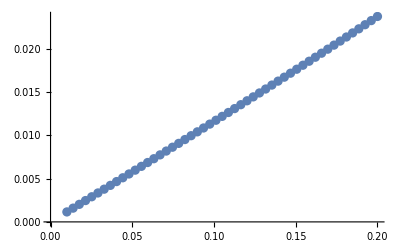

```mathematica
ListPlot[pts]
```

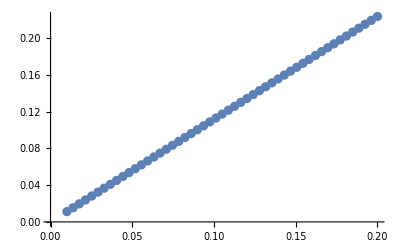

```mathematica
pts=Table[{v,Normal[Δθ[v]]}
,{v,0.01,0.2,(0.2-0.01)/50}]/.Solution/.{m->150,α->0.9 10^-6,q1->1/3,q2->-1/3,ze->1/137,a->-0.01,z->0.1};
ListPlot[pts]
```

### regge fits

```mathematica
tdata=particlesGetTraj["Meson",0,5,1,{"strange","up"}]
```

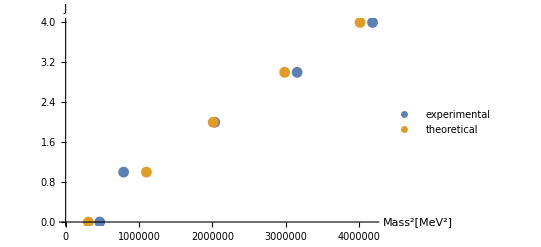

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.231515

```mathematica
pars={m->100,α->1.5 10^-6,q1-> 2/3,q2-> -1/3,ze-> 1/137,a-> -0.1,z-> 0.5 ,MeV->1};
ReleaseHold[Hold[PlotReggePoints[tdata,m,α,q1,q2,ze,a,z]]/.pars]
ReleaseHold[ReplaceAll[Hold[χsq[tdata,m,α,a,z]],pars]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

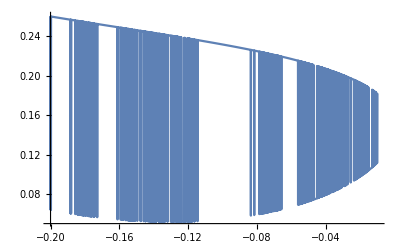

```mathematica
Plot[χsq[tdata,100,1.5 10^-6,a,0.5],{a,-0.2,-0.01}]
```

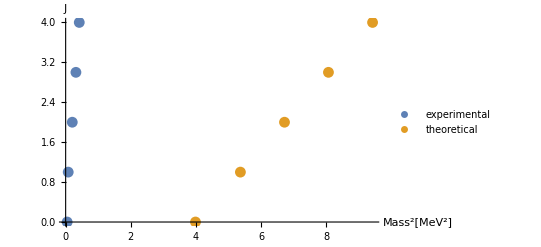

```mathematica
pars={m->10,α->1 10^-6,q1-> 1/3,q2-> -1/3,ze-> 1/137,a-> -0.1,z-> 0.7 ,MeV->1};
ReleaseHold[Hold[PlotReggePoints[tdata,m,α,q1,q2,ze,a,z]]/.pars]
```

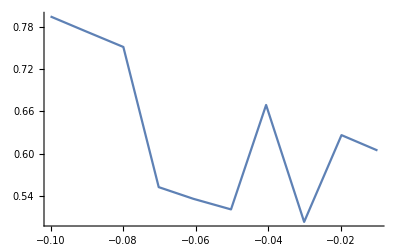
{14.33139,-Graphics-}

```mathematica
Timing[Plot[χsq[tdata,100,0.9 10^-6,a,0.3],{a,-0.1,-0.01},PlotPoints->10,MaxRecursion->0]]
```